# RG Scheme for 1- and 2-Point Functions:

## 1) Making the Coupling Vector A[i]=(K[i];p):

Here, we must declare all variables as additional couplings:

```mathematica
dim=5
A[3]=B[3]=μ;
A[4]=B[4]=η;
```

5

## 2) Determing the RG-Flow:

Sectional Partition Function before, Z0[A[i]], and after, Z1[A’[i]=B[i]]:

```mathematica
Z0[x0_,x1_,x2_]:=Exp[-A[0]]*
A[1]^(-((x0+x1)+(x1+x2))/4)*
A[2]^(-(x0*x1+x1*x2)/4)*μ^(-(x0*x2)/4)
Z1[x0_,x2_]:=Exp[-B[0]/2]*
B[1]^(-(x0+x2)/4)*
B[2]^(-(x0*x2)/4)
```

Trace:

```mathematica
TrZ0[x0_,x2_]:=Sum[Z0[x0,x1,x2],{x1,-1,1,2}]
```

Compare coeffcients:

```mathematica
i=0
For[x0=-1,x0≤1,x0+=2,
For[x2=-1,x2≤1,x2+=2,
leq[i]=Z1[x0,x2];
req[i++]=TrZ0[x0,x2];
]
]
```

0

```mathematica
leq[0]==req[0]
leq[1]==req[1]
leq[2]==req[2]
leq[3]==req[3]
```

(ⅇ^(-B[0]/2) √B[1])/B[2]^(1/4)==(ⅇ^(-A[0]) A[1])/(μ^(1/4) √A[2])+(ⅇ^(-A[0]) √A[2])/μ^(1/4)

ⅇ^(-B[0]/2) B[2]^(1/4)==(ⅇ^(-A[0]) μ^(1/4))/(√A[1])+ⅇ^(-A[0]) μ^(1/4) √A[1]

ⅇ^(-B[0]/2) B[2]^(1/4)==(ⅇ^(-A[0]) μ^(1/4))/(√A[1])+ⅇ^(-A[0]) μ^(1/4) √A[1]

ⅇ^(-B[0]/2)/(√B[1] B[2]^(1/4))==ⅇ^(-A[0])/(μ^(1/4) A[1] √A[2])+(ⅇ^(-A[0]) √A[2])/μ^(1/4)

This makes the RG-Flow:

```mathematica
SB[0]=Simplify[Solve[leq[0]*leq[1]*leq[2]*leq[3]==req[0]*req[1]*req[2]*req[3],B[0]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0][[1]]
SB[1]=Factor[Simplify[Solve[Factor[leq[0]/leq[3]]==Factor[req[0]/req[3]],B[1]]]][[1]]
SB[2]=Factor[Simplify[Solve[Factor[(leq[3]*leq[0])/(leq[1]*leq[2])]==Factor[(req[3]*req[0])/(req[1]*req[2])],B[2]]]][[1]]

SBT=Table[Part[SB[n],1],{n,0,2}];
```

{B[0]→1/2 Log[(ⅇ^(4 A[0]) A[1]^2 A[2])/((1+A[1])^2 (A[2]+A[1]^2 A[2]+A[1] (1+A[2]^2)))]}

{B[1]→(A[1] (A[1]+A[2]))/(1+A[1] A[2])}

{B[2]→(μ (1+A[1])^2 A[2])/((A[1]+A[2]) (1+A[1] A[2]))}

Raw (initial) RG-Couplings:

```mathematica
SIC={B[0]->0,B[1]->η,B[2]->μ}
```

{B[0]→0,B[1]→η,B[2]→μ}

## 3) Comparing the RG-Flow with the Partition Function:

Operators to initiate and increment the RG-Flow:

```mathematica
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}]
RG:=SAT=Table[A[n]->B[n]/.FullSimplify[SBT/.SAT,Assumptions->μ>0&&η>0],{n,0,dim-1}]
```

Final, three-spin Partition Function with renormalized couplings:

```mathematica
LnZ1=Log[Sum[Sum[Sum[
Exp[-A[0]]*
A[1]^(-((x0+x1)+(x1+x2))/4)*
A[2]^(-(x0*x1+x1*x2)/4)*
A[3]^(-(x0*x2)/4)*
A[4]^(-(x0+x2)/4),
{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
```

```mathematica
LnZ1=-A[0]+Simplify[(LnZ1/.A[0]->0),Assumptions->η>0]
```

-A[0]+Log[(1+2 √(η μ) √A[1] √A[2]+2 √(η μ) A[1]^(3/2) √A[2]+A[1] A[2]+η A[1] (A[1]+A[2]))/(μ^(1/4) A[1] √(η A[2]))]

Makes any raw Partition Function Z_k, here only used to test RG-flow:

```mathematica
θ[k_,x_,y_,z_]:=Block[{a,b},
If[k==0,
Return[η^(-(x+y+z)/2)*μ^(-(x*y+y*z+x*z)/4)],
Return[Expand[μ^(-(x*z)/4)*η^(y/2)*Sum[Sum[θ[k-1,x,a,y]*θ[k-1,y,b,z],{a,-1,1,2}],{b,-1,1,2}]]]
]
]
Z[k_]:=If[k>0,Return[Sum[Sum[Sum[θ[k-1,x,y,z],{x,-1,1,2}],{y,-1,1,2}],{z,-1,1,2}]],Return[1]]
```

Here is a test for Z_1:

```mathematica
InitRG
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[1]]
```

{A[0]→0,A[1]→η,A[2]→μ,μ→μ,η→η}

((1+η) (1-η+η^2+3 η μ))/(η^(3/2) μ^(3/4))

((1+η) (1-η+η^2+3 η μ))/(η^(3/2) μ^(3/4))

Here is a test for Z_2:

```mathematica
RG
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[2]]
```

{A[0]→1/2 Log[(η^2 μ)/((1+η)^2 (η+μ) (1+η μ))],A[1]→(η (η+μ))/(1+η μ),A[2]→((1+η)^2 μ^2)/((η+μ) (1+η μ)),μ→μ,η→η}

((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))/(η^(5/2) μ^(7/4))

((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))/(η^(5/2) μ^(7/4))

Here is a test for Z_3:

```mathematica
RG
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[3]]
```

{A[0]→3 Log[η]+2 Log[μ]-Log[(1+η) (1+η^2+2 η μ)]-1/2 Log[(η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ))],A[1]→(η^4+2 η^3 μ+η (1+η (3+η)) μ^2)/(1+η μ (2+(1+η (3+η)) μ)),A[2]→((1+η)^2 μ^3 (1+η^2+2 η μ)^2)/((η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ))),μ→μ,η→η}

1/(η^(9/2) μ^(15/4))(1+η) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)

1/(η^(9/2) μ^(15/4))(1+η) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)

```mathematica
Factor[%%/%]
```

1

Here is a test for Z_4:

```mathematica
RG
Factor[Simplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[4]]
```

$Aborted

$Aborted

$Aborted

## 4) Calculating One-Point Functions:

Defining the full W-matrix (also called the Jacobian):

```mathematica
Clear[η,μ]
MatrixForm[W=Factor[Table[D[(B[j]/.SBT),A[i]],{i,0,dim-1},{j,0,dim-1}]]]
```

(2 | 0 | 0 | 0 | 0
-((-1+A[1]) (A[1]+2 A[2]+2 A[1] A[2]+2 A[1]^2 A[2]+A[1] A[2]^2))/(2 A[1] (1+A[1]) (A[1]+A[2]) (1+A[1] A[2])) | (2 A[1]+A[2]+A[1]^2 A[2])/(1+A[1] A[2])^2 | (μ (-1+A[1]) (1+A[1]) (-1+A[2])^2 A[2])/((A[1]+A[2])^2 (1+A[1] A[2])^2) | 0 | 0
-(A[1] (-1+A[2]) (1+A[2]))/(2 A[2] (A[1]+A[2]) (1+A[1] A[2])) | -((-1+A[1]) A[1] (1+A[1]))/(1+A[1] A[2])^2 | -(μ A[1] (1+A[1])^2 (-1+A[2]) (1+A[2]))/((A[1]+A[2])^2 (1+A[1] A[2])^2) | 0 | 0
0 | 0 | ((1+A[1])^2 A[2])/((A[1]+A[2]) (1+A[1] A[2])) | 1 | 0
0 | 0 | 0 | 0 | 1)

Operators to initiate and increment the RG-Flow of Υ with the W-Matrix:

```mathematica
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
```

```mathematica
InitRGW
Υ
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
RGW;
Υ
```

{{2,0,0,0,0},{-((-1+η) (η+2 μ+2 η μ+2 η^2 μ+η μ^2))/(2 η (1+η) (η+μ) (1+η μ)),(2 η+μ+η^2 μ)/(1+η μ)^2,((-1+η) (1+η) (-1+μ)^2 μ^2)/((η+μ)^2 (1+η μ)^2),0,0},{-(η (-1+μ) (1+μ))/(2 μ (η+μ) (1+η μ)),-((-1+η) η (1+η))/(1+η μ)^2,-(η (1+η)^2 (-1+μ) μ (1+μ))/((η+μ)^2 (1+η μ)^2),0,0},{0,0,((1+η)^2 μ)/((η+μ) (1+η μ)),1,0},{0,0,0,0,1}}

First derivative of the elementary PF:

```mathematica
DLnZ1=Factor[Simplify[Table[D[LnZ1,A[i]],{i,0,dim-1}],Assumptions->μ>0&&η>0&&A[1]>0&&A[2]>0]]
```

{-1,(-1+η A[1]^2-√(η μ A[1] A[2])+√(η μ A[1]^3 A[2]))/(A[1] (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2]))),(-1-η A[1]^2+A[1] A[2]+η A[1] A[2])/(2 A[2] (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2]))),-(η (√(η μ)+η √(η μ) A[1]^2+√(η μ) A[1] A[2]+η √(η μ) A[1] A[2]-2 η μ √(A[1] A[2])-2 η μ √(A[1]^3 A[2])))/(4 (η μ)^(3/2) (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2]))),(-1+η A[1]^2-A[1] A[2]+η A[1] A[2])/(2 η (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2])))}

Test of Υ-Flow: First, for the internal energy....

```mathematica
InitRGW
dμdβ=-4μ
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
Factor[(dA0dμ.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dμdβ*D[Log[Z[1]],μ]]
Factor[%%/%]
```

-4 μ

{0,0,-4 μ,-4 μ,0}

-(3 (-1+η-η^2+η μ))/(1-η+η^2+3 η μ)

(3 (1-η+η^2-η μ))/(1-η+η^2+3 η μ)

1

```mathematica
RGW
Factor[(dA0dμ.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dμdβ*D[Log[Z[2]],μ]]
Factor[%%/%]
```

(7-7 η+7 η^2-7 η^3+7 η^4+6 η μ-6 η^2 μ+6 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)-η μ^2-3 η^2 μ^2-η^3 μ^2-12 η^2 μ^(5/2))/(1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2))

(7-7 η+7 η^2-7 η^3+7 η^4+6 η μ-6 η^2 μ+6 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)-η μ^2-3 η^2 μ^2-η^3 μ^2-12 η^2 μ^(5/2))/(1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2))

1

```mathematica
RGW
Factor[FullSimplify[(dA0dμ.Υ).(DLnZ1/.SAT),Sqrt[μ]>0&&Sqrt[η]>0]]
Factor[dμdβ*D[Log[Z[3]],μ]]
```

(-2 η^(3/2) μ^(5/2)-2 η^(7/2) μ^(5/2)-8 η^(5/2) μ^(7/2)+24 η^(9/2) μ^(7/2)+33 η^(11/2) μ^(7/2)+42 η^(13/2) μ^(7/2)+3 η^(15/2) μ^(7/2)-2 η^(5/2) μ^(9/2)-34 η^(7/2) μ^(9/2)-34 η^(11/2) μ^(9/2)-9 η^(13/2) μ^(9/2)-60 η^(7/2) μ^(11/2)-160 η^(9/2) μ^(11/2)+15 √(η μ)-15 η √(η μ)+44 η μ √(η μ)+30 η μ^2 √(η μ)+3 η μ^3 √(η μ)-44 η (η μ)^(3/2)+44 η^2 (η μ)^(3/2)-44 η^3 (η μ)^(3/2)+44 η^4 (η μ)^(3/2)-44 η^5 (η μ)^(3/2)+44 η^6 (η μ)^(3/2)+56 η μ (η μ)^(3/2)-26 η^2 μ (η μ)^(3/2)+42 η^3 μ (η μ)^(3/2)-28 η^4 μ (η μ)^(3/2)+56 η^5 μ (η μ)^(3/2)+28 η^6 μ (η μ)^(3/2)+50 η μ^2 (η μ)^(3/2)+33 η^2 μ^2 (η μ)^(3/2)-7 η μ^3 (η μ)^(3/2)-27 η^3 μ^3 (η μ)^(3/2)-60 η^4 μ^4 (η μ)^(3/2)+15 √(η^5 μ)-15 √(η^7 μ)+15 √(η^9 μ)-15 √(η^11 μ)+15 √(η^13 μ)-15 √(η^15 μ)+15 √(η^17 μ))/(√(η μ) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5))

-(-15+15 η-15 η^2+15 η^3-15 η^4+15 η^5-15 η^6+15 η^7-15 η^8-44 η μ+44 η^2 μ-44 η^3 μ+44 η^4 μ-44 η^5 μ+44 η^6 μ-44 η^7 μ-28 η μ^2-56 η^2 μ^2+28 η^3 μ^2-42 η^4 μ^2+28 η^5 μ^2-56 η^6 μ^2-28 η^7 μ^2-3 η μ^3-42 η^2 μ^3-33 η^3 μ^3-24 η^4 μ^3-33 η^5 μ^3-42 η^6 μ^3-3 η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+60 η^3 μ^5+160 η^4 μ^5+60 η^5 μ^5)/(1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)

(since it takes Mathematica forever to simplify the roots, I just choose some random value for η here)

```mathematica
FullSimplify[Factor[(%%/%)],Sqrt[η]>0&&Sqrt[μ]>0]
```

(-2 η^(3/2) μ^(5/2)+3 η^(15/2) μ^(7/2)+η^(11/2) (33-34 μ) μ^(7/2)+3 η^(13/2) (14-3 μ) μ^(7/2)-2 η^(5/2) μ^(7/2) (4+μ)+4 η^6 (η μ)^(3/2) (11+7 μ)+4 η^5 (η μ)^(3/2) (-11+14 μ)+8 η^(9/2) μ^(7/2) (3-20 μ^2)+η^3 (η μ)^(3/2) (-44+42 μ-27 μ^3)-4 η^4 (η μ)^(3/2) (-11+7 μ+15 μ^4)+15 (√(η μ)+√(η^5 μ)-√(η^7 μ)+√(η^9 μ)-√(η^11 μ)+√(η^13 μ)-√(η^15 μ)+√(η^17 μ))-2 η^(7/2) μ^(5/2) (1+μ^2 (17+30 μ))+η^2 (η μ)^(3/2) (44+μ (-26+33 μ))+η (η μ)^(3/2) (-44+μ (56+(50-7 μ) μ))+η √(η μ) (-15+μ (44+3 μ (10+μ))))/(√(η μ) (15+η (15 (-1+η) (1+η^2) (1+η^4)+44 (1+(-1+η) η (1+(-1+η) η) (1+η+η^2)) μ+14 (2+η (4+η (-2+η (3+2 η (-1+η (2+η)))))) μ^2+3 (1+η (14+η (11+η (8+η (11+η (14+η)))))) μ^3-η (9+η (34+η (27+η (34+9 η)))) μ^4-20 η^2 (3+η (8+3 η)) μ^5)))

```mathematica
Simplify[%/.η->1/3,μ>0]
```

1

...and second for the magnetization:

```mathematica
InitRGW
dηdH=-2η
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}]
Factor[(dA0dη.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dηdH*D[Log[Z[1]],η]]
Factor[%%/%]
```

-2 η

{0,-2 η,0,0,-2 η}

-(3 (-1+η) (1+η+η^2+η μ))/((1+η) (1-η+η^2+3 η μ))

-(3 (-1+√η) (1+√η) (1+η+η^2+η μ))/((1+η) (1-η+η^2+3 η μ))

1

```mathematica
RGW
Factor[(dA0dη.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dηdH*D[Log[Z[2]],η]]
Factor[%%/%]
```

-((-1+η) (5+5 η+5 η^2+5 η^3+5 η^4+6 η μ+6 η^2 μ+6 η^3 μ+6 η μ^(3/2)+8 η^2 μ^(3/2)+6 η^3 μ^(3/2)+3 η μ^2+7 η^2 μ^2+3 η^3 μ^2+4 η^2 μ^(5/2)))/((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))

-((-1+√η) (1+√η) (5+5 η+5 η^2+5 η^3+5 η^4+6 η μ+6 η^2 μ+6 η^3 μ+6 η μ^(3/2)+8 η^2 μ^(3/2)+6 η^3 μ^(3/2)+3 η μ^2+7 η^2 μ^2+3 η^3 μ^2+4 η^2 μ^(5/2)))/((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))

1

```mathematica
RGW
Factor[(dA0dη.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dηdH*D[Log[Z[3]],η]]
Factor[%%/%]
```

-((-1+η) (9+9 η+9 η^2+9 η^3+9 η^4+9 η^5+9 η^6+9 η^7+9 η^8+28 η μ+28 η^2 μ+28 η^3 μ+28 η^4 μ+28 η^5 μ+28 η^6 μ+28 η^7 μ+28 η μ^2+88 η^2 μ^2+100 η^3 μ^2+102 η^4 μ^2+100 η^5 μ^2+88 η^6 μ^2+28 η^7 μ^2+7 η μ^3+82 η^2 μ^3+157 η^3 μ^3+176 η^4 μ^3+157 η^5 μ^3+82 η^6 μ^3+7 η^7 μ^3+45 η^2 μ^4+174 η^3 μ^4+235 η^4 μ^4+174 η^5 μ^4+45 η^6 μ^4+36 η^3 μ^5+80 η^4 μ^5+36 η^5 μ^5))/((1+η) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5))

-((-1+√η) (1+√η) (9+9 η+9 η^2+9 η^3+9 η^4+9 η^5+9 η^6+9 η^7+9 η^8+28 η μ+28 η^2 μ+28 η^3 μ+28 η^4 μ+28 η^5 μ+28 η^6 μ+28 η^7 μ+28 η μ^2+88 η^2 μ^2+100 η^3 μ^2+102 η^4 μ^2+100 η^5 μ^2+88 η^6 μ^2+28 η^7 μ^2+7 η μ^3+82 η^2 μ^3+157 η^3 μ^3+176 η^4 μ^3+157 η^5 μ^3+82 η^6 μ^3+7 η^7 μ^3+45 η^2 μ^4+174 η^3 μ^4+235 η^4 μ^4+174 η^5 μ^4+45 η^6 μ^4+36 η^3 μ^5+80 η^4 μ^5+36 η^5 μ^5))/((1+η) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5))

1

## 5) Calculating Two-Point Functions:

This makes Ω as a Matrix (i,j) of vectors k: (Put k in the middle so that we can dot-product from left and right!)

```mathematica
Clear[η,μ]
Ω=Factor[Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}]]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,(-A[1]^2-2 A[1]^3+A[1]^4-4 A[1] A[2]-8 A[1]^2 A[2]-2 A[1]^3 A[2]-4 A[1]^4 A[2]+2 A[1]^5 A[2]-2 A[2]^2-4 A[1] A[2]^2-8 A[1]^2 A[2]^2-16 A[1]^3 A[2]^2+2 A[1]^6 A[2]^2-4 A[1] A[2]^3-8 A[1]^2 A[2]^3-2 A[1]^3 A[2]^3-4 A[1]^4 A[2]^3+2 A[1]^5 A[2]^3-A[1]^2 A[2]^4-2 A[1]^3 A[2]^4+A[1]^4 A[2]^4)/(2 A[1]^2 (1+A[1])^2 (A[1]+A[2])^2 (1+A[1] A[2])^2),((-1+A[1]) (1+A[1]) (-1+A[2]) (1+A[2]))/(2 (A[1]+A[2])^2 (1+A[1] A[2])^2),0,0},{0,-(2 (-1+A[2]) (1+A[2]))/(1+A[1] A[2])^3,-(-1+3 A[1]^2+A[1] A[2]+A[1]^3 A[2])/(1+A[1] A[2])^3,0,0},{0,-(2 μ (-1+A[2])^2 A[2] (-1-3 A[1] A[2]+A[1]^3 A[2]-A[2]^2))/((A[1]+A[2])^3 (1+A[1] A[2])^3),(μ (-1+A[1]) (1+A[1]) (-1+A[2]) (1+A[2]) (-A[1]+A[2]+4 A[1] A[2]+A[1]^2 A[2]-A[1] A[2]^2))/((A[1]+A[2])^3 (1+A[1] A[2])^3),((-1+A[1]) (1+A[1]) (-1+A[2])^2 A[2])/((A[1]+A[2])^2 (1+A[1] A[2])^2),0},{0,0,0,0,0},{0,0,0,0,0}},{{0,((-1+A[1]) (1+A[1]) (-1+A[2]) (1+A[2]))/(2 (A[1]+A[2])^2 (1+A[1] A[2])^2),-(A[1] (A[1]+2 A[2]+2 A[1]^2 A[2]+4 A[1] A[2]^2-A[1] A[2]^4))/(2 A[2]^2 (A[1]+A[2])^2 (1+A[1] A[2])^2),0,0},{0,-(-1+3 A[1]^2+A[1] A[2]+A[1]^3 A[2])/(1+A[1] A[2])^3,(2 (-1+A[1]) A[1]^2 (1+A[1]))/(1+A[1] A[2])^3,0,0},{0,(μ (-1+A[1]) (1+A[1]) (-1+A[2]) (1+A[2]) (-A[1]+A[2]+4 A[1] A[2]+A[1]^2 A[2]-A[1] A[2]^2))/((A[1]+A[2])^3 (1+A[1] A[2])^3),-(2 μ A[1] (1+A[1])^2 (1+A[1]^2+3 A[1] A[2]-A[1] A[2]^3))/((A[1]+A[2])^3 (1+A[1] A[2])^3),-(A[1] (1+A[1])^2 (-1+A[2]) (1+A[2]))/((A[1]+A[2])^2 (1+A[1] A[2])^2),0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,((-1+A[1]) (1+A[1]) (-1+A[2])^2 A[2])/((A[1]+A[2])^2 (1+A[1] A[2])^2),-(A[1] (1+A[1])^2 (-1+A[2]) (1+A[2]))/((A[1]+A[2])^2 (1+A[1] A[2])^2),0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
InitRGΩ:=Block[{},
InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];  This is all zero, anyway! *)
];
RGΩ:=Block[{},
Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;
];
```

```mathematica
InitRGΩ
Υ
Λ
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
RGΩ
Υ
Λ
```

{{2,0,0,0,0},{-((-1+η) (η+2 μ+2 η μ+2 η^2 μ+η μ^2))/(2 η (1+η) (η+μ) (1+η μ)),(2 η+μ+η^2 μ)/(1+η μ)^2,((-1+η) (1+η) (-1+μ)^2 μ^2)/((η+μ)^2 (1+η μ)^2),0,0},{-(η (-1+μ) (1+μ))/(2 μ (η+μ) (1+η μ)),-((-1+η) η (1+η))/(1+η μ)^2,-(η (1+η)^2 (-1+μ) μ (1+μ))/((η+μ)^2 (1+η μ)^2),0,0},{0,0,((1+η)^2 μ)/((η+μ) (1+η μ)),1,0},{0,0,0,0,1}}

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{1/(2 η^2 (1+η)^2 (η+μ)^2 (1+η μ)^2)(-η^2-2 η^3+η^4-4 η μ-8 η^2 μ-2 η^3 μ-4 η^4 μ+2 η^5 μ-2 μ^2-4 η μ^2-8 η^2 μ^2-16 η^3 μ^2+2 η^6 μ^2-4 η μ^3-8 η^2 μ^3-2 η^3 μ^3-4 η^4 μ^3+2 η^5 μ^3-η^2 μ^4-2 η^3 μ^4+η^4 μ^4),-(2 (-1+μ) (1+μ))/(1+η μ)^3,(2 (-1+μ)^2 μ^2 (1+3 η μ-η^3 μ+μ^2))/((η+μ)^3 (1+η μ)^3),0,0},{((-1+η) (1+η) (-1+μ) (1+μ))/(2 (η+μ)^2 (1+η μ)^2),(1-3 η^2-η μ-η^3 μ)/(1+η μ)^3,((-1+η) (1+η) (-1+μ) μ (1+μ) (-η+μ+4 η μ+η^2 μ-η μ^2))/((η+μ)^3 (1+η μ)^3),0,0},{0,0,((-1+η) (1+η) (-1+μ)^2 μ)/((η+μ)^2 (1+η μ)^2),0,0},{0,0,0,0,0}},{{0,0,0,0,0},{((-1+η) (1+η) (-1+μ) (1+μ))/(2 (η+μ)^2 (1+η μ)^2),(1-3 η^2-η μ-η^3 μ)/(1+η μ)^3,((-1+η) (1+η) (-1+μ) μ (1+μ) (-η+μ+4 η μ+η^2 μ-η μ^2))/((η+μ)^3 (1+η μ)^3),0,0},{-(η (η+2 μ+2 η^2 μ+4 η μ^2-η μ^4))/(2 μ^2 (η+μ)^2 (1+η μ)^2),(2 (-1+η) η^2 (1+η))/(1+η μ)^3,-(2 η (1+η)^2 μ (1+η^2+3 η μ-η μ^3))/((η+μ)^3 (1+η μ)^3),0,0},{0,0,-(η (1+η)^2 (-1+μ) (1+μ))/((η+μ)^2 (1+η μ)^2),0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,((-1+η) (1+η) (-1+μ)^2 μ)/((η+μ)^2 (1+η μ)^2),0,0},{0,0,-(η (1+η)^2 (-1+μ) (1+μ))/((η+μ)^2 (1+η μ)^2),0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

Second derivative of the elementary PF:

```mathematica
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

Test for the specific heat:

```mathematica
Clear[η,μ]
InitRGΩ
dμdβ=-4μ
d2μdβ2=16μ
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
d2A0dμ2=D[dA0dμ,μ]
η=1
```

-4 μ

16 μ

{0,0,1,1,0}

{0,0,0,0,0}

1

```mathematica
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ]
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ]
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)]
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)]
Factor[dμdβ^2*D[Log[Z[1]],{μ,2}]+d2μdβ2*D[Log[Z[1]],{μ,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,0,(-1+μ)/(2 μ (1+3 μ)),(-1+μ)/(4 μ (1+3 μ)),0}

{{0,0,0,0,0},{0,(2+μ)/(2+6 μ),0,0,1/(2+6 μ)},{0,0,(1+5 μ-2 μ^2)/(2 μ^2 (1+3 μ)^2),-(-1+μ)/(2 μ (1+3 μ)^2),0},{0,0,-(-1+μ)/(2 μ (1+3 μ)^2),(1+4 μ-μ^2)/(4 μ^2 (1+3 μ)^2),0},{0,1/(2+6 μ),0,0,(1+μ)/(4+12 μ)}}

0

(12 (-1+μ))/(1+3 μ)

0

-(12 (-1-6 μ+3 μ^2))/(1+3 μ)^2

(48 μ)/(1+3 μ)^2

1

```mathematica
RGΩ
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ]
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ]
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)]
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)]
Factor[dμdβ^2*D[Log[Z[2]],{μ,2}]+d2μdβ2*D[Log[Z[2]],{μ,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,0,((1+μ)^2 (-1-2 μ+3 μ^2))/(8 μ^2 (1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2))),(-1-2 μ+4 μ^(3/2)-5 μ^2+4 μ^(5/2))/(4 μ (1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2))),0}

{{0,0,0,0,0},{0,((1+μ) (1+μ+μ^(3/2)))/(1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2)),0,0,(1+μ)^2/(2+4 μ+8 μ^(3/2)+10 μ^2+8 μ^(5/2))},{0,0,-((1+μ)^4 (-1-4 μ-6 μ^(3/2)-14 μ^2-18 μ^(5/2)-20 μ^3-10 μ^(7/2)+7 μ^4+2 μ^(9/2)))/(32 μ^4 (1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2))^2),-((1+μ)^3 (-1-2 μ+3 μ^2))/(4 μ^(3/2) (1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2))^2),0},{0,0,-((1+μ)^3 (-1-2 μ+3 μ^2))/(4 μ^(3/2) (1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2))^2),(1+4 μ+4 μ^(3/2)+14 μ^2+12 μ^(5/2)+4 μ^3+28 μ^(7/2)-7 μ^4+20 μ^(9/2)-16 μ^5)/(4 μ^2 (1+2 μ+4 μ^(3/2)+5 μ^2+4 μ^(5/2))^2),0},{0,(1+μ)^2/(2+4 μ+8 μ^(3/2)+10 μ^2+8 μ^(5/2)),0,0,(1+2 μ+5 μ^2)/(4+8 μ+16 μ^(3/2)+20 μ^2+16 μ^(5/2))}}

0

(4 (-1+√μ) (7+7 √μ+13 μ+17 μ^(3/2)+12 μ^2))/((1+√μ) (1-√μ+3 μ+μ^(3/2)+4 μ^2))

-(8 (1-√μ-3 μ-μ^(3/2)-21 μ^2+9 μ^(5/2)-5 μ^3+μ^(7/2)+4 μ^4))/((1+μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2))

-(4 (-9-38 μ-68 μ^(3/2)-135 μ^2-228 μ^(5/2)-196 μ^3-168 μ^(7/2)+41 μ^4-8 μ^(9/2)+26 μ^5-20 μ^(11/2)+39 μ^6-20 μ^(13/2)+16 μ^7))/((1+√μ)^2 (1+μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2)^2)

(16 μ (2+9 √μ+20 μ+27 μ^(3/2)+10 μ^2+23 μ^(5/2)+16 μ^3+5 μ^(7/2)))/((1+√μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2)^2)

1

```mathematica
RGΩ
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ]
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ]
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)]
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)]
Factor[dμdβ^2*D[Log[Z[3]],{μ,2}]+d2μdβ2*D[Log[Z[3]],{μ,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,0,((1+2 μ+5 μ^2)^2 (-1-4 μ-14 μ^2-4 μ^3+7 μ^4+16 μ^5))/(32 μ^3 (1+μ)^2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)),-(1+4 μ+6 μ^2+12 μ^3+μ^4-24 μ^5)/(4 μ (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)),0}

{{0,0,0,0,0},{0,((1+2 μ+5 μ^2) (1+2 μ+7 μ^2+2 μ^3))/(1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5),0,0,((1+2 μ+5 μ^2)^2)/(2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5))},{0,0,-((1+2 μ+5 μ^2)^4 (-1-8 μ-56 μ^2-268 μ^3-994 μ^4-2572 μ^5-4624 μ^6-5028 μ^7-3221 μ^8-188 μ^9+576 μ^10))/(512 μ^6 (1+μ)^4 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2),-((1+2 μ+5 μ^2)^3 (-1-4 μ-14 μ^2-4 μ^3+7 μ^4+16 μ^5))/(8 μ^2 (1+μ) (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2),0},{0,0,-((1+2 μ+5 μ^2)^5 (-2+(32 μ^3 (1+μ)^2)/(1+μ (2+5 μ))^2))/(16 μ^2 (1+μ) (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2),(1+8 μ+52 μ^2+240 μ^3+798 μ^4+2000 μ^5+3812 μ^6+5296 μ^7+4361 μ^8+520 μ^9-704 μ^10)/(4 μ^2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2),0},{0,((1+2 μ+5 μ^2)^2)/(2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)),0,0,(1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)/(4+16 μ+88 μ^2+240 μ^3+452 μ^4+224 μ^5)}}

0

(4 (-1+μ) (15+59 μ+213 μ^2+393 μ^3+280 μ^4))/(1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)

-(16 (1+4 μ-67 μ^2-608 μ^3-2886 μ^4-7760 μ^5-13734 μ^6-16216 μ^7-10459 μ^8-1652 μ^9+2825 μ^10+1400 μ^11))/((1+μ)^2 (1+2 μ+5 μ^2)^2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5))

-(4 (-19-242 μ-1961 μ^2-11876 μ^3-55403 μ^4-199278 μ^5-549513 μ^6-1161160 μ^7-1896097 μ^8-2451886 μ^9-2550915 μ^10-2116164 μ^11-1357345 μ^12-482866 μ^13+25013 μ^14+148400 μ^15+78400 μ^16))/((1+μ)^2 (1+2 μ+5 μ^2)^2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)

(64 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/((1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)

1

```mathematica
RGΩ
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ]
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ]
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)]
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)]
Factor[dμdβ^2*D[Log[Z[4]],{μ,2}]+d2μdβ2*D[Log[Z[4]],{μ,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,0,((1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2 (-2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2))/(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2 (2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(32 μ^(5/2) (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))),-(2 √μ+(128 μ^(9/2) (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2-(32 μ^3 (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))/(4 μ^(3/2) (2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(32 μ^(5/2) (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))),0}

{{0,0,0,0,0},{0,((1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5) (1+4 μ+14 μ^2+4 μ^(5/2)+36 μ^3+12 μ^(7/2)+57 μ^4+28 μ^(9/2)+16 μ^5+20 μ^(11/2)))/(1+8 μ+44 μ^2+16 μ^(5/2)+184 μ^3+112 μ^(7/2)+662 μ^4+528 μ^(9/2)+1880 μ^5+1776 μ^(11/2)+4492 μ^6+4528 μ^(13/2)+7880 μ^7+8144 μ^(15/2)+9457 μ^8+10032 μ^(17/2)+6304 μ^9+6352 μ^(19/2)+1856 μ^10+1280 μ^(21/2)),0,0,(1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^2/(2 (1+8 μ+44 μ^2+16 μ^(5/2)+184 μ^3+112 μ^(7/2)+662 μ^4+528 μ^(9/2)+1880 μ^5+1776 μ^(11/2)+4492 μ^6+4528 μ^(13/2)+7880 μ^7+8144 μ^(15/2)+9457 μ^8+10032 μ^(17/2)+6304 μ^9+6352 μ^(19/2)+1856 μ^10+1280 μ^(21/2)))},{0,0,-(512 μ^(13/2) (1+μ)^3 (1+2 μ+5 μ^2)^3 (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)-24 μ^(5/2) (1+3 μ+7 μ^2+5 μ^3) (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^3+4096 μ^8 (1+μ)^4 (1+μ (2+5 μ))^4-128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2 (1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2-(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^4)/(2048 μ^8 (1+μ)^4 (1+μ (2+5 μ))^4 (2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(32 μ^(5/2) (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))^2),((1+2 μ+5 μ^2)^3 (1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^4 (2-(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2))/(8 μ^(5/2) (1+μ) (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^3 (1+μ (2+5 μ))^4 (2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(32 μ^(5/2) (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))^2),0},{0,0,-((1+μ (4+μ (14+μ (36+μ (57+16 μ))))) (-2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2))/(8 μ^(5/2) (1+μ) (1+μ (2+5 μ)) (2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(32 μ^(5/2) (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))^2),(1024 μ^(13/2) (1+μ)^3 (1+2 μ+5 μ^2)^3 (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)-256 μ^5 (1+3 μ+7 μ^2+5 μ^3)^2 (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^2+16 μ^(5/2) (1+3 μ+7 μ^2+5 μ^3) (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^3+4096 μ^8 (1+μ)^4 (1+μ (2+5 μ))^4+128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2 (1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^4)/(μ^2 (1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^4 (2+(128 μ^4 (1+μ)^2 (1+μ (2+5 μ))^2)/(1+μ (4+μ (14+μ (36+μ (57+16 μ)))))^2+(32 μ^(5/2) (1+μ) (1+μ (2+5 μ)))/(1+μ (4+μ (14+μ (36+μ (57+16 μ))))))^2),0},{0,(1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^2/(2 (1+8 μ+44 μ^2+16 μ^(5/2)+184 μ^3+112 μ^(7/2)+662 μ^4+528 μ^(9/2)+1880 μ^5+1776 μ^(11/2)+4492 μ^6+4528 μ^(13/2)+7880 μ^7+8144 μ^(15/2)+9457 μ^8+10032 μ^(17/2)+6304 μ^9+6352 μ^(19/2)+1856 μ^10+1280 μ^(21/2))),0,0,(1+8 μ+44 μ^2+184 μ^3+662 μ^4+1880 μ^5+4492 μ^6+7880 μ^7+9457 μ^8+6304 μ^9+1856 μ^10)/(4 (1+8 μ+44 μ^2+16 μ^(5/2)+184 μ^3+112 μ^(7/2)+662 μ^4+528 μ^(9/2)+1880 μ^5+1776 μ^(11/2)+4492 μ^6+4528 μ^(13/2)+7880 μ^7+8144 μ^(15/2)+9457 μ^8+10032 μ^(17/2)+6304 μ^9+6352 μ^(19/2)+1856 μ^10+1280 μ^(21/2)))}}

0

(4 (-1+√μ) (31+31 √μ+247 μ+247 μ^(3/2)+1259 μ^2+1595 μ^(5/2)+5091 μ^3+6995 μ^(7/2)+16925 μ^4+23789 μ^(9/2)+44469 μ^5+60453 μ^(11/2)+91897 μ^6+114537 μ^(13/2)+138177 μ^7+146321 μ^(15/2)+136864 μ^8+106768 μ^(17/2)+75248 μ^9+30784 μ^(19/2)+14080 μ^10))/((1+√μ) (1-√μ+9 μ-9 μ^(3/2)+53 μ^2-37 μ^(5/2)+221 μ^3-109 μ^(7/2)+771 μ^4-243 μ^(9/2)+2123 μ^5-347 μ^(11/2)+4839 μ^6-311 μ^(13/2)+8191 μ^7-47 μ^(15/2)+9504 μ^8+528 μ^(17/2)+5776 μ^9+576 μ^(19/2)+1280 μ^10))

-(8 (1-√μ+7 μ-7 μ^(3/2)-230 μ^2+54 μ^(5/2)-5794 μ^3+2098 μ^(7/2)-72263 μ^4+28423 μ^(9/2)-621033 μ^5+247785 μ^(11/2)-4112776 μ^6+1611448 μ^(13/2)-22114696 μ^7+8330040 μ^(15/2)-99439678 μ^8+35355454 μ^(17/2)-380639250 μ^9+125387538 μ^(19/2)-1254552388 μ^10+374910308 μ^(21/2)-3585779436 μ^11+948525708 μ^(23/2)-8922213638 μ^12+2028787334 μ^(25/2)-19342444474 μ^13+3646623418 μ^(27/2)-36452405480 μ^14+5436657224 μ^(29/2)-59381703512 μ^15+6564427448 μ^(31/2)-82785519395 μ^16+6146554147 μ^(33/2)-97176203989 μ^17+4078482389 μ^(35/2)-93554286790 μ^18+1494974038 μ^(37/2)-70647426114 μ^19+17331218 μ^(39/2)-38276658259 μ^20+206149651 μ^(41/2)-11307753853 μ^21+1043984509 μ^(43/2)+1804104032 μ^22+1252730128 μ^(45/2)+3716857008 μ^23+729143616 μ^(47/2)+1807207680 μ^24+201062400 μ^(49/2)+428748800 μ^25+18432000 μ^(51/2)+40960000 μ^26))/((1+μ)^2 (1+2 μ+5 μ^2)^2 (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^2 (1-√μ+9 μ-9 μ^(3/2)+53 μ^2-37 μ^(5/2)+221 μ^3-109 μ^(7/2)+771 μ^4-243 μ^(9/2)+2123 μ^5-347 μ^(11/2)+4839 μ^6-311 μ^(13/2)+8191 μ^7-47 μ^(15/2)+9504 μ^8+528 μ^(17/2)+5776 μ^9+576 μ^(19/2)+1280 μ^10))

-(4 (-33-958 μ-15027 μ^2-912 μ^(5/2)-166012 μ^3-25616 μ^(7/2)-1438429 μ^4-387936 μ^(9/2)-10351786 μ^5-4123360 μ^(11/2)-64083167 μ^6-34124784 μ^(13/2)-349133944 μ^7-232230384 μ^(15/2)-1699866429 μ^8-1343070656 μ^(17/2)-7472933678 μ^9-6745083328 μ^(19/2)-29866057591 μ^10-29859546256 μ^(21/2)-108983247492 μ^11-117778551824 μ^(23/2)-364068482777 μ^12-417249218464 μ^(25/2)-1115101199786 μ^13-1335587076128 μ^(27/2)-3134220423459 μ^14-3880370421104 μ^(29/2)-8087948696048 μ^15-10268564007024 μ^(31/2)-19166667105011 μ^16-24816097209728 μ^(33/2)-41712287872586 μ^17-54878471041152 μ^(35/2)-83341721458665 μ^18-111201264001328 μ^(37/2)-152750947520708 μ^19-206625680564400 μ^(39/2)-256384930548871 μ^20-352079485910176 μ^(41/2)-392878438372302 μ^21-549649358830880 μ^(43/2)-546837329361165 μ^22-784464209217616 μ^(45/2)-685753869572024 μ^23-1019575426989136 μ^(47/2)-765102293984239 μ^24-1199447013536704 μ^(49/2)-744379717246922 μ^25-1265791626609088 μ^(51/2)-609711521975341 μ^26-1182979015257776 μ^(53/2)-390105908847548 μ^27-961438954131248 μ^(55/2)-152554524302339 μ^28-662585105409120 μ^(57/2)+28400105749026 μ^29-374390948785120 μ^(59/2)+111178629770575 μ^30-166381305114192 μ^(61/2)+107800054410656 μ^31-55879339730256 μ^(63/2)+65629477566592 μ^32-14381253173504 μ^(65/2)+27382133707008 μ^33-3458149348352 μ^(67/2)+7833818312704 μ^34-920817418240 μ^(69/2)+1509515591680 μ^35-182760243200 μ^(71/2)+186096025600 μ^36-15204352000 μ^(73/2)+10485760000 μ^37))/((1+√μ)^2 (1+μ)^2 (1+2 μ+5 μ^2)^2 (1+4 μ+14 μ^2+36 μ^3+57 μ^4+16 μ^5)^2 (1-√μ+9 μ-9 μ^(3/2)+53 μ^2-37 μ^(5/2)+221 μ^3-109 μ^(7/2)+771 μ^4-243 μ^(9/2)+2123 μ^5-347 μ^(11/2)+4839 μ^6-311 μ^(13/2)+8191 μ^7-47 μ^(15/2)+9504 μ^8+528 μ^(17/2)+5776 μ^9+576 μ^(19/2)+1280 μ^10)^2)

(64 μ (2+44 μ+25 μ^(3/2)+502 μ^2+415 μ^(5/2)+4120 μ^3+4117 μ^(7/2)+25690 μ^4+29323 μ^(9/2)+130164 μ^5+163301 μ^(11/2)+546150 μ^6+734067 μ^(13/2)+1933904 μ^7+2748977 μ^(15/2)+5880974 μ^8+8681119 μ^(17/2)+15561556 μ^9+23275243 μ^(19/2)+35906482 μ^10+52847277 μ^(21/2)+71555480 μ^11+101098799 μ^(23/2)+121500398 μ^12+160969041 μ^(25/2)+172969612 μ^13+209613863 μ^(27/2)+200784882 μ^14+216149825 μ^(29/2)+182371456 μ^15+167862475 μ^(31/2)+122725160 μ^16+92249669 μ^(33/2)+56937728 μ^17+31890096 μ^(35/2)+15766016 μ^18+5275712 μ^(37/2)+2032640 μ^19+148480 μ^(39/2)))/((1+√μ)^2 (1-√μ+9 μ-9 μ^(3/2)+53 μ^2-37 μ^(5/2)+221 μ^3-109 μ^(7/2)+771 μ^4-243 μ^(9/2)+2123 μ^5-347 μ^(11/2)+4839 μ^6-311 μ^(13/2)+8191 μ^7-47 μ^(15/2)+9504 μ^8+528 μ^(17/2)+5776 μ^9+576 μ^(19/2)+1280 μ^10)^2)

1

Test for the susceptibility:

```mathematica
Clear[η,μ]
InitRGΩ
dηdH=-2η
d2ηdH2=4η
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}]
d2A0dη2=D[dA0dη,η]
```

-2 η

4 η

{0,1,0,0,1}

{0,0,0,0,0}

```mathematica
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ]
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ]
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)]
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)]
Factor[dηdH^2*D[Log[Z[1]],{η,2}]+d2ηdH2*D[Log[Z[1]],{η,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,((-1+η) (1+η+η^2+η μ))/(η+η^4+3 η^2 μ+3 η^3 μ),(-1+η-η^2+η μ)/(2 μ (1+η^2+η (-1+3 μ))),(-1+η-η^2+η μ)/(4 μ (1+η^2+η (-1+3 μ))),((-1+η) (1+η+η^2+η μ))/(2 η (1+η^3+3 η μ+3 η^2 μ))}

{{0,0,0,0,0},{0,(2-2 η^6+11 η μ-5 η^5 μ+η^4 (7-5 μ) μ+η^2 μ (15+7 μ)+2 η^3 (4+5 μ^2))/(2 (η+η^4+3 η^2 μ+3 η^3 μ)^2),-((-1+η^2) (3+3 η^2+η (5+μ)))/(2 (1+η^3+3 η μ+3 η^2 μ)^2),-((-1+η^2) (1+η^2-η (-3+μ)))/(2 (1+η^3+3 η μ+3 η^2 μ)^2),(μ+η^4 μ-η (-5+μ) μ-η^3 (-5+μ) μ+2 η^2 (2+μ^2))/(2 η (1+η^3+3 η μ+3 η^2 μ)^2)},{0,-((-1+η^2) (3+3 η^2+η (5+μ)))/(2 (1+η^3+3 η μ+3 η^2 μ)^2),(1+η^4+η (-2+5 μ)+η^3 (-2+5 μ)+η^2 (3-5 μ-2 μ^2))/(2 μ^2 (1+η^2+η (-1+3 μ))^2),((√(η^9 μ^5)+√(η^11 μ^5)) (1+η^2-η (1+μ)))/(2 (1+η) (η μ)^(7/2) (1+η^2+η (-1+3 μ))^2),-((-1+η) (1+η) (1+η^2-η (-3+μ)))/(2 (1+η^3+3 η μ+3 η^2 μ)^2)},{0,-((-1+η^2) (1+η^2-η (-3+μ)))/(2 (1+η^3+3 η μ+3 η^2 μ)^2),(η (1+η^2-η (1+μ)))/(2 μ (1+η^2+η (-1+3 μ))^2),(4 η^(9/2) μ^(7/2)+4 η^(17/2) μ^(7/2)-η^(11/2) (-4+μ) μ^(7/2)-η^(15/2) (-4+μ) μ^(7/2)+√(η^7 μ^5)+√(η^19 μ^5)-2 η^(13/2) μ^(5/2) (-1+μ^2))/(4 η^(7/2) μ^(9/2) (1+η^3+3 η μ+3 η^2 μ)^2),-((-1+η) (1+η) (1+η+η^2+η μ))/(2 (1+η^3+3 η μ+3 η^2 μ)^2)},{0,(μ+η^4 μ-η (-5+μ) μ-η^3 (-5+μ) μ+2 η^2 (2+μ^2))/(2 η (1+η^3+3 η μ+3 η^2 μ)^2),-((-1+η) (1+η) (1+η^2-η (-3+μ)))/(2 (1+η^3+3 η μ+3 η^2 μ)^2),-((-1+η) (1+η+η^2+η μ) (√(η^7 μ^5)+√(η^9 μ^5)))/(2 η^(7/2) μ^(5/2) (1+η^3+3 η μ+3 η^2 μ)^2),(1-η^6+5 η μ-3 η^5 μ+η^2 μ (5+4 μ)+η^4 (μ-2 μ^2)+η^3 (2+4 μ^2))/(2 (η+η^4+3 η^2 μ+3 η^3 μ)^2)}}

0

(6 (-1+η) (1+η+η^2+η μ))/((1+η) (1-η+η^2+3 η μ))

0

-(6 (-1-6 η^3+η^6-6 η μ-10 η^2 μ-6 η^4 μ+2 η^5 μ-3 η^2 μ^2-6 η^3 μ^2+3 η^4 μ^2))/((1+η)^2 (1-η+η^2+3 η μ)^2)

(12 η (3 η^2+μ+4 η μ+4 η^3 μ+η^4 μ+3 η^2 μ^2))/((1+η)^2 (1-η+η^2+3 η μ)^2)

1

```mathematica
RGΩ
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ]
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ]
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)]
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)]
Factor[dηdH^2*D[Log[Z[2]],{η,2}]+d2ηdH2*D[Log[Z[2]],{η,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,((-1+η) (1+η μ) (1+η^4+η (1+2 μ+μ^(3/2))+η^3 (1+2 μ+μ^(3/2))+η^2 (1+2 μ+2 μ^(3/2)+μ^2)))/(η (η+μ) (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ))),-((η+μ) (1+η μ) (1+η^4-η (-1+μ)^2-η^3 (-1+μ)^2-η^2 (-1+2 μ+μ^2)))/(2 (1+η)^2 μ^2 (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))),(η (2 η^(3/2) μ^2+2 η^(9/2) μ^2-√(η μ)-4 (η μ)^(5/2)-4 η (η μ)^(5/2)-√(η^11 μ)-(η μ)^(3/2) (2+μ)-η^3 (η μ)^(3/2) (2+μ)+2 η^(5/2) μ^2 (1+2 μ)+2 η^(7/2) μ^2 (1+2 μ)))/(4 (1+η) (η μ)^(3/2) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))),(-1+η^5-2 η^2 μ^2+2 η^3 μ^2-η μ (2+μ)+η^4 μ (2+μ))/(2 η (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ)))}

{{0,0,0,0,0},{0,-((1+η μ)^2 (η^3 (1+η)^3 μ^(7/2) (η+μ)+η^4 (1+η)^3 μ^(7/2) (η+μ)+4 η^4 (1+η)^2 μ^3 (η+μ)^2+5 η^5 (1+η) μ^(3/2) (η+μ)^3+2 η^6 (η+μ)^4-3 η^2 (1+η)^3 μ^(7/2) (1+η μ)-3 η^3 (1+η)^3 μ^(7/2) (1+η μ)-8 η^3 (1+η)^2 μ^3 (η+μ) (1+η μ)-7 η^4 (1+η) μ^(3/2) (η+μ)^2 (1+η μ)-4 η (1+η)^2 μ^2 (1+η μ)^2-4 η^2 (1+η)^2 μ^2 (1+η μ)^2-4 η^2 (1+η)^2 μ^3 (1+η μ)^2-11 η^2 (1+η) μ^(3/2) (η+μ) (1+η μ)^2-8 η^3 (η+μ)^2 (1+η μ)^2-7 η (1+η) μ^(3/2) (1+η μ)^3-2 (1+η μ)^4))/(2 η^2 (η+μ)^2 (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ))^2),-((-1+η) (1+η μ)^2 (1+η^6 (1+2 √μ)+2 √μ+η (1+6 √μ+6 μ+4 μ^(3/2)+μ^2)+η^5 (1+6 √μ+6 μ+4 μ^(3/2)+μ^2)+η^2 (4+8 √μ+6 μ+12 μ^(3/2)+13 μ^2+2 μ^(5/2))+η^4 (4+8 √μ+6 μ+12 μ^(3/2)+13 μ^2+2 μ^(5/2))+4 η^3 (1+2 √μ+3 μ+4 μ^(3/2)+3 μ^2+μ^(5/2)+μ^3)))/(2 (1+η)^3 √μ (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),-((-1+η) √μ (1+η μ) (1+η^6+η (1+6 μ-μ^2)+η^5 (1+6 μ-μ^2)+η^2 (4+6 μ+5 μ^2)+η^4 (4+6 μ+5 μ^2)+4 η^3 (1+3 μ+μ^3)))/(2 (1+η) (η+μ) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),((1+η μ)^2 (-η (1+η)^3 μ^(7/2)+η^2 (1+η)^3 μ^(7/2)+3 η^3 (1+η) μ^(3/2) (η+μ)^2+(η^2 (1+η)^3 μ^(7/2) (η+μ))/(1+η μ)-(η^3 (1+η)^3 μ^(7/2) (η+μ))/(1+η μ)+(2 η^3 (1+η)^2 μ^2 (η+μ)^2)/(1+η μ)+(η^4 (1+η) μ^(3/2) (η+μ)^3)/(1+η μ)+2 η (1+η)^2 μ^2 (1+η μ)+3 η (1+η) μ^(3/2) (η+μ) (1+η μ)+4 η^2 (η+μ)^2 (1+η μ)+(1+η) μ^(3/2) (1+η μ)^2))/(2 η (η+μ) (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ))^2)},{0,-((-1+η) (1+η μ)^2 (1+η^6 (1+2 √μ)+2 √μ+η (1+6 √μ+6 μ+4 μ^(3/2)+μ^2)+η^5 (1+6 √μ+6 μ+4 μ^(3/2)+μ^2)+η^2 (4+8 √μ+6 μ+12 μ^(3/2)+13 μ^2+2 μ^(5/2))+η^4 (4+8 √μ+6 μ+12 μ^(3/2)+13 μ^2+2 μ^(5/2))+4 η^3 (1+2 √μ+3 μ+4 μ^(3/2)+3 μ^2+μ^(5/2)+μ^3)))/(2 (1+η)^3 √μ (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),-((η+μ)^2 (1+η μ)^2 (η^2 (1+η)^4 μ^4+2 η^3 (1+η)^4 μ^4+η^4 (1+η)^4 μ^4+η^3 (1+η)^3 μ^(7/2) (η+μ)+η^4 (1+η)^3 μ^(7/2) (η+μ)-2 η^4 (1+η)^2 μ^2 (η+μ)^2-2 η^5 (1+η)^2 μ^2 (η+μ)^2-3 η^5 (1+η) μ^(3/2) (η+μ)^3-η^6 (η+μ)^4+η^2 (1+η)^3 μ^(7/2) (1+η μ)+η^3 (1+η)^3 μ^(7/2) (1+η μ)-3 η^4 (1+η) μ^(3/2) (η+μ)^2 (1+η μ)-2 η (1+η)^2 μ^2 (1+η μ)^2-2 η^2 (1+η)^2 μ^2 (1+η μ)^2-3 η^2 (1+η) μ^(3/2) (η+μ) (1+η μ)^2-2 η^3 (η+μ)^2 (1+η μ)^2-3 η (1+η) μ^(3/2) (1+η μ)^3-(1+η μ)^4))/(2 (1+η)^4 μ^4 (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ))^2),(η (η+μ) (1+η μ) (1+η^2+2 η μ) (1+η^4-η (-1+μ)^2-η^3 (-1+μ)^2-η^2 (-1+2 μ+μ^2)))/(2 (1+η)^2 μ^(3/2) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),-((η+μ) (1+η μ) (-1+η^7+η^4 (2+4 √μ-μ) μ+η^3 μ (-2-4 √μ+μ)+η^6 (2 √μ+4 μ-μ^2)+η (-2 √μ-4 μ+μ^2)+η^5 (1+2 √μ+4 μ^(3/2)+4 μ^2-2 μ^3)+η^2 (-1-2 √μ-4 μ^(3/2)-4 μ^2+2 μ^3)))/(2 (1+η)^3 √μ (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2)},{0,-((-1+η) √μ (1+η μ) (1+η^6+η (1+6 μ-μ^2)+η^5 (1+6 μ-μ^2)+η^2 (4+6 μ+5 μ^2)+η^4 (4+6 μ+5 μ^2)+4 η^3 (1+3 μ+μ^3)))/(2 (1+η) (η+μ) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),(η (1+η μ) (η+η^3+μ+3 η^2 μ+2 η μ^2) (1+η^4-η (-1+μ)^2-η^3 (-1+μ)^2-η^2 (-1+2 μ+μ^2)))/(2 (1+η)^2 μ^(3/2) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),(2 η^(3/2) μ^2+√(η μ)+4 η^6 (η μ)^(3/2)+3 √(η^5 μ)-4 √(η^7 μ)+5 √(η^9 μ)-4 √(η^11 μ)+3 √(η^13 μ)-2 √(η^15 μ)+√(η^17 μ)+√(η^13 μ^9)+2 η^5 (η μ)^(3/2) (-4+3 μ)-2 η^4 (η μ)^(3/2) (-6+5 μ)+4 η (η μ)^(3/2) (-2+2 μ+μ^2)+2 η √(η μ) (-1+2 μ+μ^2)+2 η^(13/2) μ^2 (-1+√μ+4 μ+μ^2)+2 η^2 (η μ)^(3/2) (6-5 μ+4 μ^2)+2 η^(15/2) (μ^2+μ^(5/2))+η^(5/2) μ^2 (-2+8 μ-4 μ^(3/2)+2 μ^2+μ^(5/2))+2 η^(7/2) μ^2 (2-4 μ+7 μ^2-5 μ^(5/2)+2 μ^3)+2 η^(11/2) μ^2 (2-4 μ+4 μ^(3/2)+7 μ^2-5 μ^(5/2)+2 μ^3)+η^3 (η μ)^(3/2) (-12+14 μ+11 μ^3)-4 η^(9/2) μ^2 (1-3 μ+3 μ^(3/2)+μ^2-3 μ^3+4 μ^(7/2)))/(4 μ^2 √(η μ) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),-(√μ (1+η^2+2 η μ) (-1+η^5-2 η^2 μ^2+2 η^3 μ^2-η μ (2+μ)+η^4 μ (2+μ)))/(2 (1+η) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2)},{0,-((1+η μ)^2 (η (1+η)^3 μ^(7/2)-η^2 (1+η)^3 μ^(7/2)-3 η^3 (1+η) μ^(3/2) (η+μ)^2-(η^2 (1+η)^3 μ^(7/2) (η+μ))/(1+η μ)+(η^3 (1+η)^3 μ^(7/2) (η+μ))/(1+η μ)-(2 η^3 (1+η)^2 μ^2 (η+μ)^2)/(1+η μ)-(η^4 (1+η) μ^(3/2) (η+μ)^3)/(1+η μ)-2 η (1+η)^2 μ^2 (1+η μ)-3 η (1+η) μ^(3/2) (η+μ) (1+η μ)-4 η^2 (η+μ)^2 (1+η μ)-(1+η) μ^(3/2) (1+η μ)^2))/(2 η (η+μ) (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ))^2),-((η+μ) (1+η μ) (-1+η^7+η^4 (2+4 √μ-μ) μ+η^3 μ (-2-4 √μ+μ)+η^6 (2 √μ+4 μ-μ^2)+η (-2 √μ-4 μ+μ^2)+η^5 (1+2 √μ+4 μ^(3/2)+4 μ^2-2 μ^3)+η^2 (-1-2 √μ-4 μ^(3/2)-4 μ^2+2 μ^3)))/(2 (1+η)^3 √μ (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),-((-1+η) √μ (1+η^6+η (1+4 μ+μ^2)+η^5 (1+4 μ+μ^2)+η^2 (2+4 μ+7 μ^2+2 μ^3)+η^4 (2+4 μ+7 μ^2+2 μ^3)+η^3 (2+6 μ+6 μ^2+6 μ^3)))/(2 (1+η) (1+η^4+η (-1+2 μ+2 μ^(3/2)+μ^2)+η^3 (-1+2 μ+2 μ^(3/2)+μ^2)+η^2 (1-2 μ+3 μ^2+4 μ^(5/2)))^2),-(-η^2 (1+η)^4 μ^4-2 η^3 (1+η)^4 μ^4+η^4 (1+η)^4 μ^4-3 η^3 (1+η)^3 μ^(7/2) (η+μ)+η^4 (1+η)^3 μ^(7/2) (η+μ)-2 η^4 (1+η)^2 μ^2 (η+μ)^2+2 η^5 (1+η)^2 μ^2 (η+μ)^2+η^5 (1+η) μ^(3/2) (η+μ)^3+η^6 (η+μ)^4-3 η^2 (1+η)^3 μ^(7/2) (1+η μ)+η^3 (1+η)^3 μ^(7/2) (1+η μ)+η^4 (1+η) μ^(3/2) (η+μ)^2 (1+η μ)-2 η (1+η)^2 μ^2 (1+η μ)^2-2 η^2 (1+η)^2 μ^2 (1+η μ)^2-3 η^2 (1+η) μ^(3/2) (η+μ) (1+η μ)^2-2 η^3 (η+μ)^2 (1+η μ)^2-3 η (1+η) μ^(3/2) (1+η μ)^3-(1+η μ)^4)/(2 η^2 (1+η^5+η μ (2+2 √μ+μ)+η^4 μ (2+2 √μ+μ)+2 η^2 μ^(3/2) (1+2 √μ+2 μ)+2 η^3 μ^(3/2) (1+2 √μ+2 μ))^2)}}

0

(2 (-1+η) (5+5 η+5 η^2+5 η^3+5 η^4+6 η μ+6 η^2 μ+6 η^3 μ+6 η μ^(3/2)+8 η^2 μ^(3/2)+6 η^3 μ^(3/2)+3 η μ^2+7 η^2 μ^2+3 η^3 μ^2+4 η^2 μ^(5/2)))/((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))

-(2 (5 η^2+η^3+4 η^4-4 η^5+4 η^6-7 η^7-3 η^8-4 η^2 μ+22 η^3 μ-14 η^4 μ+24 η^5 μ-38 η^6 μ-2 η^7 μ-4 η^8 μ+2 η^3 μ^(3/2)+4 η^4 μ^(3/2)-12 η^6 μ^(3/2)-2 η^7 μ^(3/2)-2 μ^2-2 η μ^2-6 η^2 μ^2-41 η^3 μ^2+47 η^4 μ^2-80 η^5 μ^2+27 η^6 μ^2-29 η^7 μ^2+2 η^8 μ^2+2 η^9 μ^2+2 η^10 μ^2-4 η^2 μ^(5/2)-8 η^3 μ^(5/2)-16 η^4 μ^(5/2)-40 η^5 μ^(5/2)-8 η^7 μ^(5/2)+4 η^8 μ^(5/2)-12 η μ^3-20 η^2 μ^3-12 η^3 μ^3-112 η^4 μ^3+40 η^5 μ^3-72 η^6 μ^3+20 η^7 μ^3+4 η^8 μ^3+4 η^9 μ^3-4 η μ^(7/2)-8 η^2 μ^(7/2)-40 η^3 μ^(7/2)-80 η^4 μ^(7/2)-24 η^5 μ^(7/2)-40 η^6 μ^(7/2)+16 η^7 μ^(7/2)+4 η^9 μ^(7/2)-2 η μ^4-25 η^2 μ^4-53 η^3 μ^4-12 η^4 μ^4-84 η^5 μ^4+24 η^6 μ^4-13 η^7 μ^4+3 η^8 μ^4+2 η^9 μ^4-20 η^2 μ^(9/2)-40 η^3 μ^(9/2)-44 η^4 μ^(9/2)-80 η^5 μ^(9/2)+4 η^6 μ^(9/2)-8 η^7 μ^(9/2)+12 η^8 μ^(9/2)-4 η^2 μ^5-18 η^3 μ^5-38 η^4 μ^5-8 η^5 μ^5-22 η^6 μ^5+6 η^7 μ^5+4 η^8 μ^5-18 η^3 μ^(11/2)-36 η^4 μ^(11/2)-8 η^5 μ^(11/2)-20 η^6 μ^(11/2)+10 η^7 μ^(11/2)-3 η^3 μ^6-7 η^4 μ^6-8 η^5 μ^6+η^6 μ^6+η^7 μ^6-4 η^4 μ^(13/2)-8 η^5 μ^(13/2)+4 η^6 μ^(13/2)))/((1+η)^2 (η+μ)^2 (1+η μ)^2 (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))

-(2 (-10 η^2+4 η^3-8 η^4+12 η^5-16 η^6-32 η^7-16 η^8+12 η^9-8 η^10+4 η^11+8 η^12-10 η μ+4 η^2 μ-66 η^3 μ+48 η^4 μ-80 η^5 μ-52 η^6 μ-120 η^7 μ-52 η^8 μ-80 η^9 μ+48 η^10 μ+26 η^11 μ+4 η^12 μ+10 η^13 μ-32 η^3 μ^(3/2)-32 η^4 μ^(3/2)-60 η^5 μ^(3/2)-52 η^6 μ^(3/2)-24 η^7 μ^(3/2)-32 η^8 μ^(3/2)-40 η^9 μ^(3/2)+20 η^10 μ^(3/2)+20 η^11 μ^(3/2)-3 μ^2-54 η^2 μ^2+28 η^3 μ^2-263 η^4 μ^2-42 η^5 μ^2-352 η^6 μ^2-148 η^7 μ^2-336 η^8 μ^2+10 η^9 μ^2-13 η^10 μ^2+48 η^11 μ^2+42 η^12 μ^2+3 η^14 μ^2-36 η^2 μ^(5/2)-44 η^3 μ^(5/2)-264 η^4 μ^(5/2)-248 η^5 μ^(5/2)-260 η^6 μ^(5/2)-224 η^7 μ^(5/2)-196 η^8 μ^(5/2)+8 η^9 μ^(5/2)-8 η^10 μ^(5/2)+12 η^11 μ^(5/2)+20 η^12 μ^(5/2)-14 η μ^3-12 η^2 μ^3-206 η^3 μ^3-120 η^4 μ^3-664 η^5 μ^3-316 η^6 μ^3-824 η^7 μ^3-124 η^8 μ^3-192 η^9 μ^3+32 η^10 μ^3+46 η^11 μ^3+12 η^12 μ^3+14 η^13 μ^3-12 η μ^(7/2)-20 η^2 μ^(7/2)-224 η^3 μ^(7/2)-264 η^4 μ^(7/2)-720 η^5 μ^(7/2)-656 η^6 μ^(7/2)-660 η^7 μ^(7/2)-172 η^8 μ^(7/2)-172 η^9 μ^(7/2)-4 η^10 μ^(7/2)+16 η^11 μ^(7/2)-4 η^12 μ^(7/2)+4 η^13 μ^(7/2)-6 η μ^4-58 η^2 μ^4-108 η^3 μ^4-426 η^4 μ^4-482 η^5 μ^4-1178 η^6 μ^4-396 η^7 μ^4-650 η^8 μ^4-118 η^9 μ^4+20 η^10 μ^4+12 η^11 μ^4+16 η^12 μ^4+2 η^13 μ^4-60 η^2 μ^(9/2)-112 η^3 μ^(9/2)-516 η^4 μ^(9/2)-600 η^5 μ^(9/2)-1088 η^6 μ^(9/2)-528 η^7 μ^(9/2)-608 η^8 μ^(9/2)-128 η^9 μ^(9/2)-44 η^10 μ^(9/2)-24 η^11 μ^(9/2)+4 η^12 μ^(9/2)-16 η^2 μ^5-102 η^3 μ^5-288 η^4 μ^5-626 η^5 μ^5-512 η^6 μ^5-968 η^7 μ^5-320 η^8 μ^5-158 η^9 μ^5-64 η^10 μ^5+30 η^11 μ^5+16 η^12 μ^5-4 η^2 μ^(11/2)-112 η^3 μ^(11/2)-228 η^4 μ^(11/2)-596 η^5 μ^(11/2)-436 η^6 μ^(11/2)-856 η^7 μ^(11/2)-256 η^8 μ^(11/2)-200 η^9 μ^(11/2)-72 η^10 μ^(11/2)+12 η^11 μ^(11/2)+4 η^12 μ^(11/2)-η^2 μ^6-32 η^3 μ^6-102 η^4 μ^6-250 η^5 μ^6-493 η^6 μ^6-308 η^7 μ^6-339 η^8 μ^6-126 η^9 μ^6+38 η^10 μ^6+20 η^11 μ^6+η^12 μ^6-12 η^3 μ^(13/2)-92 η^4 μ^(13/2)-168 η^5 μ^(13/2)-420 η^6 μ^(13/2)-152 η^7 μ^(13/2)-268 η^8 μ^(13/2)-72 η^9 μ^(13/2)+20 η^10 μ^(13/2)+4 η^11 μ^(13/2)-2 η^3 μ^7-32 η^4 μ^7-78 η^5 μ^7-104 η^6 μ^7-152 η^7 μ^7-72 η^8 μ^7-10 η^9 μ^7+2 η^11 μ^7-20 η^4 μ^(15/2)-68 η^5 μ^(15/2)-56 η^6 μ^(15/2)-124 η^7 μ^(15/2)-20 η^8 μ^(15/2)+8 η^9 μ^(15/2)-8 η^5 μ^8-24 η^6 μ^8-20 η^7 μ^8-4 η^8 μ^8+4 η^9 μ^8+2 η^10 μ^8-8 η^5 μ^(17/2)-24 η^6 μ^(17/2)-8 η^7 μ^(17/2)))/((1+η)^2 (η+μ)^2 (1+η μ)^2 (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2))^2)

(4 η (25 η^4+2 μ+32 η^3 μ+32 η^5 μ+2 η^8 μ+2 μ^(3/2)+8 η μ^(3/2)+18 η^2 μ^(3/2)+32 η^3 μ^(3/2)+32 η^5 μ^(3/2)+18 η^6 μ^(3/2)+8 η^7 μ^(3/2)+2 η^8 μ^(3/2)+μ^2+16 η μ^2+36 η^2 μ^2+16 η^3 μ^2+36 η^4 μ^2+16 η^5 μ^2+36 η^6 μ^2+16 η^7 μ^2+η^8 μ^2+16 η μ^(5/2)+40 η^2 μ^(5/2)+16 η^3 μ^(5/2)+72 η^4 μ^(5/2)+16 η^5 μ^(5/2)+40 η^6 μ^(5/2)+16 η^7 μ^(5/2)+12 η^2 μ^3+48 η^3 μ^3+76 η^4 μ^3+48 η^5 μ^3+12 η^6 μ^3+18 η^2 μ^(7/2)+72 η^3 μ^(7/2)+52 η^4 μ^(7/2)+72 η^5 μ^(7/2)+18 η^6 μ^(7/2)+12 η^2 μ^4+48 η^3 μ^4+41 η^4 μ^4+48 η^5 μ^4+12 η^6 μ^4+4 η^2 μ^(9/2)+16 η^3 μ^(9/2)+32 η^4 μ^(9/2)+16 η^5 μ^(9/2)+4 η^6 μ^(9/2)+16 η^4 μ^5))/((1+η)^2 (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2))^2)

1

```mathematica
RGΩ
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0]
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0]
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ]
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ]
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)]
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)]
Factor[dηdH^2*D[Log[Z[3]],{η,2}]+d2ηdH2*D[Log[Z[3]],{η,1}]]
Factor[(term0+term1+term2+term3)/%]
```

{-1,((1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (-1+η^9-η μ (4+3 μ)+η^8 μ (4+3 μ)-η^2 μ^2 (11+8 μ+μ^2)+η^7 μ^2 (11+8 μ+μ^2)-η^4 μ^2 (1+4 μ+9 μ^2)+η^5 μ^2 (1+4 μ+9 μ^2)-η^3 μ^2 (3+16 μ+9 μ^2)+η^6 μ^2 (3+16 μ+9 μ^2)))/(η (1+η) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η^8+η (-1+4 μ+4 μ^2+μ^3)+η^7 (-1+4 μ+4 μ^2+μ^3)+η^2 (1-4 μ+8 μ^2+14 μ^3+9 μ^4)+η^6 (1-4 μ+8 μ^2+14 μ^3+9 μ^4)+η^3 (-1+4 μ-4 μ^2+11 μ^3+34 μ^4+12 μ^5)+η^5 (-1+4 μ-4 μ^2+11 μ^3+34 μ^4+12 μ^5)+η^4 (1-4 μ+6 μ^2+8 μ^3+27 μ^4+32 μ^5))),((η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ)) (-1-η^9+η μ (-4-2 μ+μ^2)+η^8 μ (-4-2 μ+μ^2)+η^2 μ^2 (-10-μ+3 μ^2)+η^7 μ^2 (-10-μ+3 μ^2)+η^4 μ^3 (3-μ+12 μ^2)+η^5 μ^3 (3-μ+12 μ^2)+η^3 μ^2 (-2-7 μ+5 μ^2+4 μ^3)+η^6 μ^2 (-2-7 μ+5 μ^2+4 μ^3)))/(2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))),-(η (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (√(η μ)+((1+η)^2 μ^2 (η μ)^(3/2) (1+η^2+2 η μ)^2)/((1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2)+((1+η)^2 μ (η μ)^(5/2) (1+η^2+2 η μ)^2)/((1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2)-(2 η^(3/2) (1+η) μ^(5/2) (1+η^2+2 η μ))/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-(2 (1+η) (η μ)^(5/2) (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)))/((1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2)+(η √(η μ) (η^4+2 η^3 μ+η (1+η (3+η)) μ^2)^2)/(1+η μ (2+(1+η (3+η)) μ))^2))/(4 (η μ)^(3/2) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))),(-1+η^9-5 η^2 μ^2 (2+μ+μ^2)+5 η^7 μ^2 (2+μ+μ^2)-η μ (4+2 μ+μ^2)+η^8 μ (4+2 μ+μ^2)-η^4 μ^3 (5+5 μ+4 μ^2)+η^5 μ^3 (5+5 μ+4 μ^2)-η^3 μ^2 (2+13 μ+9 μ^2+4 μ^3)+η^6 μ^2 (2+13 μ+9 μ^2+4 μ^3))/(2 η (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3)))}

{{0,0,0,0,0},{0,-((1+η μ (2+(1+η (3+η)) μ))^2 (-3 η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-3 η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-4 η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-4 η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-4 η^2 (1+η)^2 μ^4 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-7 η (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3-2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^4+η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+η^4 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-8 η^3 (1+η)^2 μ^4 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-11 η^2 (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+4 η^4 (1+η)^2 μ^4 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-7 η^4 (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-8 η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+5 η^5 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3+2 η^6 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^4))/(2 (η^4+2 η^3 μ+η (1+η (3+η)) μ^2)^2 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-((-1+η) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (1+2 μ+η^12 (1+2 μ)+η (1+12 μ+18 μ^2+5 μ^3)+η^11 (1+12 μ+18 μ^2+5 μ^3)+η^2 (1+16 μ+72 μ^2+76 μ^3+31 μ^4+2 μ^5)+η^10 (1+16 μ+72 μ^2+76 μ^3+31 μ^4+2 μ^5)+η^3 (1+26 μ+98 μ^2+245 μ^3+220 μ^4+62 μ^5+8 μ^6)+η^9 (1+26 μ+98 μ^2+245 μ^3+220 μ^4+62 μ^5+8 μ^6)+η^4 (4+28 μ+138 μ^2+360 μ^3+565 μ^4+314 μ^5+76 μ^6)+η^8 (4+28 μ+138 μ^2+360 μ^3+565 μ^4+314 μ^5+76 μ^6)+4 η^6 (1+10 μ+44 μ^2+120 μ^3+220 μ^4+207 μ^5+91 μ^6)+2 η^5 (2+20 μ+76 μ^2+233 μ^3+393 μ^4+340 μ^5+124 μ^6)+2 η^7 (2+20 μ+76 μ^2+233 μ^3+393 μ^4+340 μ^5+124 μ^6)))/(2 (1+η) μ (1+η^2+2 η μ) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-((1+η) (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^(11/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+η^(13/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-η^(9/2) μ^(11/2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3-η^(13/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η^(15/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-3 (η μ)^(11/2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+3 η^(15/2) μ^(11/2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^(17/2) μ^(11/2) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3))/(2 (η μ)^(9/2) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ)) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),((1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^7 (-η (1+η)^3 μ^5 (1+η^2+2 η μ)^3+η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3+2 η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+(1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2+(η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)))/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-(η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)))/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+3 η (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+3 η^3 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+(2 η^3 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2)/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+4 η^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+(η^4 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3)/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))))/(2 η (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ))^5 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2)},{0,-((-1+η) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (1+2 μ+η^12 (1+2 μ)+η (1+12 μ+18 μ^2+5 μ^3)+η^11 (1+12 μ+18 μ^2+5 μ^3)+η^2 (1+16 μ+72 μ^2+76 μ^3+31 μ^4+2 μ^5)+η^10 (1+16 μ+72 μ^2+76 μ^3+31 μ^4+2 μ^5)+η^3 (1+26 μ+98 μ^2+245 μ^3+220 μ^4+62 μ^5+8 μ^6)+η^9 (1+26 μ+98 μ^2+245 μ^3+220 μ^4+62 μ^5+8 μ^6)+η^4 (4+28 μ+138 μ^2+360 μ^3+565 μ^4+314 μ^5+76 μ^6)+η^8 (4+28 μ+138 μ^2+360 μ^3+565 μ^4+314 μ^5+76 μ^6)+4 η^6 (1+10 μ+44 μ^2+120 μ^3+220 μ^4+207 μ^5+91 μ^6)+2 η^5 (2+20 μ+76 μ^2+233 μ^3+393 μ^4+340 μ^5+124 μ^6)+2 η^7 (2+20 μ+76 μ^2+233 μ^3+393 μ^4+340 μ^5+124 μ^6)))/(2 (1+η) μ (1+η^2+2 η μ) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-((η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2 (1+η μ (2+(1+η (3+η)) μ))^2 (η^2 (1+η)^4 μ^6 (1+η^2+2 η μ)^4+2 η^3 (1+η)^4 μ^6 (1+η^2+2 η μ)^4+η^4 (1+η)^4 μ^6 (1+η^2+2 η μ)^4+η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-2 η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-2 η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-3 η (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3-(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^4+η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+η^4 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-3 η^2 (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-2 η^4 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-2 η^5 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-3 η^4 (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-2 η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-3 η^5 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3-η^6 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^4))/(2 (1+η)^4 μ^6 (1+η^2+2 η μ)^4 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),((η^4+2 η^3 μ+η (1+η (3+η)) μ^2) (1+η^4+6 η^2 μ^2+2 η μ (1+μ)+2 η^3 μ (1+μ)) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (1+η^9+η^4 μ^3 (-3+μ-12 μ^2)+η^5 μ^3 (-3+μ-12 μ^2)+η^2 μ^2 (10+μ-3 μ^2)+η^7 μ^2 (10+μ-3 μ^2)+η μ (4+2 μ-μ^2)+η^8 μ (4+2 μ-μ^2)+η^3 μ^2 (2+7 μ-5 μ^2-4 μ^3)+η^6 μ^2 (2+7 μ-5 μ^2-4 μ^3)))/(2 (1+η) μ^2 (1+η^2+2 η μ) (1+η μ (2+(1+η (3+η)) μ)) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-((η^4+2 η^3 μ+η (1+η (3+η)) μ^2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-2 η (1+η) μ (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3+η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η^3 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+2 η^3 (1+η) μ (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^4 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3))/(2 η (1+η) μ (1+η^2+2 η μ) (1+η μ (2+(1+η (3+η)) μ)) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2)},{0,-((1+η) μ (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3-η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η^3 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-3 η (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+3 η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^4 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3))/(2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ)) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-((η^4+2 η^3 μ+η (1+η (3+η)) μ^2) (1+η^4+6 η^2 μ^2+2 η μ (1+μ)+2 η^3 μ (1+μ)) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (-1-η^9+η μ (-4-2 μ+μ^2)+η^8 μ (-4-2 μ+μ^2)+η^2 μ^2 (-10-μ+3 μ^2)+η^7 μ^2 (-10-μ+3 μ^2)+η^4 μ^3 (3-μ+12 μ^2)+η^5 μ^3 (3-μ+12 μ^2)+η^3 μ^2 (-2-7 μ+5 μ^2+4 μ^3)+η^6 μ^2 (-2-7 μ+5 μ^2+4 μ^3)))/(2 (1+η) μ^2 (1+η^2+2 η μ) (1+η μ (2+(1+η (3+η)) μ)) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),(η^(11/2) (1+η)^4 μ^(21/2) (1+η^2+2 η μ)^4+2 η^(13/2) (1+η)^4 μ^(21/2) (1+η^2+2 η μ)^4+η^(15/2) (1+η)^4 μ^(21/2) (1+η^2+2 η μ)^4+2 η^(11/2) (1+η)^3 μ^(19/2) (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+2 η^(13/2) (1+η)^3 μ^(19/2) (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+2 η^(9/2) (1+η)^2 μ^(15/2) (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2+2 η^(11/2) (1+η)^2 μ^(15/2) (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-4 η^(11/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-η^(9/2) (1+η) μ^(13/2) (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3+3 (1+η) μ^2 (η μ)^(9/2) (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3+η^(7/2) μ^(9/2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^4+2 η^(13/2) (1+η)^3 μ^(19/2) (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+2 η^(15/2) (1+η)^3 μ^(19/2) (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-8 η^(13/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+2 η^(11/2) (1+η) μ^(13/2) (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+2 η^(17/2) (1+η)^2 μ^(15/2) (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-4 η^(15/2) (1+η)^2 μ^(17/2) (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+2 (1+η)^2 (η μ)^(15/2) (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+2 η^(15/2) (1+η) μ^(13/2) (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+2 η^(13/2) μ^(9/2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+2 η^(17/2) (1+η) μ^(13/2) (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3+η^(19/2) μ^(9/2) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^4)/(4 μ^3 (η μ)^(7/2) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-(μ (1+η^2+2 η μ) (1+η^4+6 η^2 μ^2+2 η μ (1+μ)+2 η^3 μ (1+μ)) (-1+η^9-5 η^2 μ^2 (2+μ+μ^2)+5 η^7 μ^2 (2+μ+μ^2)-η μ (4+2 μ+μ^2)+η^8 μ (4+2 μ+μ^2)-η^4 μ^3 (5+5 μ+4 μ^2)+η^5 μ^3 (5+5 μ+4 μ^2)-η^3 μ^2 (2+13 μ+9 μ^2+4 μ^3)+η^6 μ^2 (2+13 μ+9 μ^2+4 μ^3)))/(2 (1+η) (1+η^8+η (-1+4 μ+4 μ^2+μ^3)+η^7 (-1+4 μ+4 μ^2+μ^3)+η^2 (1-4 μ+8 μ^2+14 μ^3+9 μ^4)+η^6 (1-4 μ+8 μ^2+14 μ^3+9 μ^4)+η^3 (-1+4 μ-4 μ^2+11 μ^3+34 μ^4+12 μ^5)+η^5 (-1+4 μ-4 μ^2+11 μ^3+34 μ^4+12 μ^5)+η^4 (1-4 μ+6 μ^2+8 μ^3+27 μ^4+32 μ^5))^2)},{0,-((1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^7 (η (1+η)^3 μ^5 (1+η^2+2 η μ)^3-η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3-2 η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-(1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-(η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)))/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+(η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)))/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-3 η (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-3 η^3 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-(2 η^3 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2)/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-4 η^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-(η^4 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3)/(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))))/(2 η (η^3+μ^2+3 η μ^2+η^2 μ (2+μ)) (1+η μ (2+(1+η (3+η)) μ))^5 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-((η^4+2 η^3 μ+η (1+η (3+η)) μ^2) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-2 η (1+η) μ (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3+η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η^3 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+2 η^3 (1+η) μ (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^4 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3))/(2 η (1+η) μ (1+η^2+2 η μ) (1+η μ (2+(1+η (3+η)) μ)) (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),((1+η) μ (1+η^2+2 η μ) (η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3+η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η^3 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+η (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-η^4 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3))/(2 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2),-(-η^2 (1+η)^4 μ^6 (1+η^2+2 η μ)^4-2 η^3 (1+η)^4 μ^6 (1+η^2+2 η μ)^4+η^4 (1+η)^4 μ^6 (1+η^2+2 η μ)^4-3 η^2 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))+η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))-2 η (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-2 η^2 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2-3 η (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^3-(1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^4-3 η^3 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))+η^4 (1+η)^3 μ^5 (1+η^2+2 η μ)^3 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-3 η^2 (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))-2 η^4 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+2 η^5 (1+η)^2 μ^3 (1+η^2+2 η μ)^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^4 (1+η) μ^2 (1+η^2+2 η μ) (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ)) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2-2 η^3 (1+3 η^2 μ^2+η^3 μ^2+η μ (2+μ))^2 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^2+η^5 (1+η) μ^2 (1+η^2+2 η μ) (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^3+η^6 (η^3+μ^2+3 η μ^2+η^2 μ (2+μ))^4)/(2 η^2 (1+η^9+η μ (2+μ)^2+η^8 μ (2+μ)^2+3 η^2 μ^2 (4+5 μ+3 μ^2)+3 η^7 μ^2 (4+5 μ+3 μ^2)+η^3 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^6 μ^2 (4+25 μ+43 μ^2+12 μ^3)+η^4 μ^2 (2+19 μ+61 μ^2+44 μ^3)+η^5 μ^2 (2+19 μ+61 μ^2+44 μ^3))^2)}}

0

(2 (-1+η) (9+9 η+9 η^2+9 η^3+9 η^4+9 η^5+9 η^6+9 η^7+9 η^8+28 η μ+28 η^2 μ+28 η^3 μ+28 η^4 μ+28 η^5 μ+28 η^6 μ+28 η^7 μ+28 η μ^2+88 η^2 μ^2+100 η^3 μ^2+102 η^4 μ^2+100 η^5 μ^2+88 η^6 μ^2+28 η^7 μ^2+7 η μ^3+82 η^2 μ^3+157 η^3 μ^3+176 η^4 μ^3+157 η^5 μ^3+82 η^6 μ^3+7 η^7 μ^3+45 η^2 μ^4+174 η^3 μ^4+235 η^4 μ^4+174 η^5 μ^4+45 η^6 μ^4+36 η^3 μ^5+80 η^4 μ^5+36 η^5 μ^5))/((1+η) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5))

-(2 (33 η^6+21 η^7+46 η^8+30 η^9+37 η^10+17 η^11+16 η^12-16 η^13+16 η^14-31 η^15-11 η^16-66 η^17-50 η^18-27 η^19-15 η^20+88 η^5 μ+48 η^6 μ+464 η^7 μ+280 η^8 μ+540 η^9 μ+292 η^10 μ+356 η^11 μ-4 η^12 μ+224 η^13 μ-340 η^14 μ+20 η^15 μ-700 η^16 μ-452 η^17 μ-504 η^18 μ-320 η^19 μ-80 η^20 μ-40 η^21 μ+110 η^4 μ^2+70 η^5 μ^2+1028 η^6 μ^2+728 η^7 μ^2+3256 η^8 μ^2+1996 η^9 μ^2+3210 η^10 μ^2+1128 η^11 μ^2+2000 η^12 μ^2-1316 η^13 μ^2+208 η^14 μ^2-4340 η^15 μ^2-2414 η^16 μ^2-3956 η^17 μ^2-2384 η^18 μ^2-1332 η^19 μ^2-764 η^20 μ^2-170 η^21 μ^2-66 η^22 μ^2-8 η^2 μ^3+48 η^3 μ^3-28 η^4 μ^3+1004 η^5 μ^3+1016 η^6 μ^3+6065 η^7 μ^3+4876 η^8 μ^3+14054 η^9 μ^3+7688 η^10 μ^3+11867 η^11 μ^3-480 η^12 μ^3+2300 η^13 μ^3-15760 η^14 μ^3-10121 η^15 μ^3-20096 η^16 μ^3-12186 η^17 μ^3-9916 η^18 μ^3-5459 η^19 μ^3-2216 η^20 μ^3-980 η^21 μ^3-124 η^22 μ^3-32 η^23 μ^3+8 η^24 μ^3-6 μ^4-30 η μ^4-39 η^2 μ^4-227 η^3 μ^4+168 η^4 μ^4-148 η^5 μ^4+4157 η^6 μ^4+4925 η^7 μ^4+20549 η^8 μ^4+15318 η^9 μ^4+38081 η^10 μ^4+9712 η^11 μ^4+13482 η^12 μ^4-37172 η^13 μ^4-32086 η^14 μ^4-68592 η^15 μ^4-48267 η^16 μ^4-48382 η^17 μ^4-28019 η^18 μ^4-15475 η^19 μ^4-6507 η^20 μ^4-1388 η^21 μ^4-336 η^22 μ^4+109 η^23 μ^4+41 η^24 μ^4+30 η^25 μ^4+6 η^26 μ^4-80 η μ^5-444 η^2 μ^5-788 η^3 μ^5-2348 η^4 μ^5-2494 η^5 μ^5-4780 η^6 μ^5+3260 η^7 μ^5+2532 η^8 μ^5+32060 η^9 μ^5+584 η^10 μ^5+24972 η^11 μ^5-72584 η^12 μ^5-83612 η^13 μ^5-177016 η^14 μ^5-152404 η^15 μ^5-164632 η^16 μ^5-107668 η^17 μ^5-71180 η^18 μ^5-32116 η^19 μ^5-10020 η^20 μ^5-2070 η^21 μ^5+732 η^22 μ^5+508 η^23 μ^5+324 η^24 μ^5+64 η^25 μ^5-40 η μ^6-774 η^2 μ^6-3818 η^3 μ^6-8654 η^4 μ^6-19434 η^5 μ^6-32606 η^6 μ^6-52826 η^7 μ^6-62998 η^8 μ^6-104856 η^9 μ^6-103772 η^10 μ^6-230376 η^11 μ^6-244448 η^12 μ^6-407468 η^13 μ^6-408720 η^14 μ^6-445624 η^15 μ^6-334972 η^16 μ^6-239584 η^17 μ^6-120286 η^18 μ^6-47110 η^19 μ^6-11622 η^20 μ^6+1742 η^21 μ^6+2874 η^22 μ^6+1946 η^23 μ^6+498 η^24 μ^6+32 η^25 μ^6-6 η μ^7-496 η^2 μ^7-5279 η^3 μ^7-22364 η^4 μ^7-54864 η^5 μ^7-113372 η^6 μ^7-202585 η^7 μ^7-329880 η^8 μ^7-465170 η^9 μ^7-669904 η^10 μ^7-788620 η^11 μ^7-1014616 η^12 μ^7-1032000 η^13 μ^7-1066280 η^14 μ^7-885676 η^15 μ^7-664192 η^16 μ^7-381030 η^17 μ^7-174104 η^18 μ^7-52789 η^19 μ^7+108 η^20 μ^7+10984 η^21 μ^7+8348 η^22 μ^7+2821 η^23 μ^7+352 η^24 μ^7+6 η^25 μ^7-165 η^2 μ^8-3715 η^3 μ^8-27423 η^4 μ^8-101560 η^5 μ^8-249672 η^6 μ^8-495430 η^7 μ^8-847727 η^8 μ^8-1299338 η^9 μ^8-1741931 η^10 μ^8-2184189 η^11 μ^8-2392914 η^12 μ^8-2438192 η^13 μ^8-2125266 η^14 μ^8-1637645 η^15 μ^8-1048771 η^16 μ^8-546362 η^17 μ^8-209939 η^18 μ^8-32054 η^19 μ^8+25968 η^20 μ^8+27712 η^21 μ^8+12169 η^22 μ^8+2269 η^23 μ^8+127 η^24 μ^8-12 η^2 μ^9-1330 η^3 μ^9-18340 η^4 μ^9-106650 η^5 μ^9-351364 η^6 μ^9-818158 η^7 μ^9-1531596 η^8 μ^9-2432772 η^9 μ^9-3409908 η^10 μ^9-4178348 η^11 μ^9-4550140 η^12 μ^9-4346084 η^13 μ^9-3610124 η^14 μ^9-2555628 η^15 μ^9-1490372 η^16 μ^9-681620 η^17 μ^9-182356 η^18 μ^9+28810 η^19 μ^9+68124 η^20 μ^9+37966 η^21 μ^9+9436 η^22 μ^9+902 η^23 μ^9+12 η^24 μ^9-196 η^3 μ^10-6302 η^4 μ^10-62224 η^5 μ^10-303424 η^6 μ^10-904484 η^7 μ^10-1957360 η^8 μ^10-3399388 η^9 μ^10-4934358 η^10 μ^10-6173524 η^11 μ^10-6676136 η^12 μ^10-6207376 η^13 μ^10-4978264 η^14 μ^10-3331320 η^15 μ^10-1797998 η^16 μ^10-667372 η^17 μ^10-71896 η^18 μ^10+113388 η^19 μ^10+88104 η^20 μ^10+28424 η^21 μ^10+3978 η^22 μ^10+160 η^23 μ^10-7 η^3 μ^11-1136 η^4 μ^11-20512 η^5 μ^11-154548 η^6 μ^11-642142 η^7 μ^11-1721676 η^8 μ^11-3394386 η^9 μ^11-5338312 η^10 μ^11-6924483 η^11 μ^11-7572536 η^12 μ^11-7028068 η^13 μ^11-5416856 η^14 μ^11-3409439 η^15 μ^11-1592016 η^16 μ^11-415554 η^17 μ^11+81948 η^18 μ^11+137474 η^19 μ^11+58100 η^20 μ^11+10872 η^21 μ^11+744 η^22 μ^11+5 η^23 μ^11-71 η^4 μ^12-3408 η^5 μ^12-43596 η^6 μ^12-268242 η^7 μ^12-968952 η^8 μ^12-2325984 η^9 μ^12-4114741 η^10 μ^12-5740872 η^11 μ^12-6478500 η^12 μ^12-5952228 η^13 μ^12-4418372 η^14 μ^12-2480232 η^15 μ^12-909941 η^16 μ^12-71888 η^17 μ^12+141912 η^18 μ^12+84462 η^19 μ^12+20772 η^20 μ^12+2144 η^21 μ^12+57 η^22 μ^12-260 η^5 μ^13-6440 η^6 μ^13-61804 η^7 μ^13-317408 η^8 μ^13-1000404 η^9 μ^13-2119880 η^10 μ^13-3263976 η^11 μ^13-3850200 η^12 μ^13-3513688 η^13 μ^13-2404792 η^14 μ^13-1144072 η^15 μ^13-267656 η^16 μ^13+69820 η^17 μ^13+78704 η^18 μ^13+25492 η^19 μ^13+3592 η^20 μ^13+172 η^21 μ^13-348 η^6 μ^14-6400 η^7 μ^14-50168 η^8 μ^14-220264 η^9 μ^14-602676 η^10 μ^14-1092528 η^11 μ^14-1372500 η^12 μ^14-1224792 η^13 μ^14-753812 η^14 μ^14-265776 η^15 μ^14-3828 η^16 μ^14+42776 η^17 μ^14+18696 η^18 μ^14+3392 η^19 μ^14+228 η^20 μ^14-144 η^7 μ^15-2272 η^8 μ^15-15488 η^9 μ^15-59168 η^10 μ^15-138048 η^11 μ^15-201568 η^12 μ^15-180384 η^13 μ^15-88864 η^14 μ^15-12352 η^15 μ^15+10528 η^16 μ^15+6272 η^17 μ^15+1376 η^18 μ^15+112 η^19 μ^15))/((1+η)^2 (1+η^2+2 η μ)^2 (η^3+2 η^2 μ+μ^2+3 η μ^2+η^2 μ^2)^2 (1+2 η μ+η μ^2+3 η^2 μ^2+η^3 μ^2)^2 (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5))

-(2 (-42 η^6+12 η^7-76 η^8+28 η^9-74 η^10+48 η^11-64 η^12+80 η^13-96 η^14-68 η^15-104 η^16-200 η^17-104 η^18-68 η^19-96 η^20+80 η^21-64 η^22+48 η^23-8 η^24+28 η^25+56 η^26+12 η^27+24 η^28-124 η^5 μ+40 η^6 μ-852 η^7 μ+272 η^8 μ-1284 η^9 μ+584 η^10 μ-1196 η^11 μ+1024 η^12 μ-1312 η^13 μ+328 η^14 μ-1712 η^15 μ-2248 η^16 μ-1792 η^17 μ-2248 η^18 μ-1712 η^19 μ+328 η^20 μ-1312 η^21 μ+1024 η^22 μ-468 η^23 μ+584 η^24 μ+636 η^25 μ+272 η^26 μ+540 η^27 μ+40 η^28 μ+76 η^29 μ-18 η^3 μ^2-200 η^4 μ^2-14 η^5 μ^2-2176 η^6 μ^2+224 η^7 μ^2-8280 η^8 μ^2+1940 η^9 μ^2-10924 η^10 μ^2+4890 η^11 μ^2-11252 η^12 μ^2+4222 η^13 μ^2-13980 η^14 μ^2-9096 η^15 μ^2-17224 η^16 μ^2-20996 η^17 μ^2-17088 η^18 μ^2-8892 η^19 μ^2-13580 η^20 μ^2+4922 η^21 μ^2-6264 η^22 μ^2+6510 η^23 μ^2+3416 η^24 μ^2+3656 η^25 μ^2+4932 η^26 μ^2+1020 η^27 μ^2+1512 η^28 μ^2+158 η^29 μ^2+156 η^30 μ^2+18 η^31 μ^2-28 η^2 μ^3-164 η^3 μ^3-312 η^4 μ^3-3184 η^5 μ^3-1380 η^6 μ^3-18872 η^7 μ^3-3160 η^8 μ^3-51984 η^9 μ^3+3532 η^10 μ^3-67032 η^11 μ^3+8352 η^12 μ^3-80028 η^13 μ^3-30724 η^14 μ^3-104940 η^15 μ^3-102264 η^16 μ^3-118196 η^17 μ^3-100160 η^18 μ^3-99512 η^19 μ^3-21756 η^20 μ^3-52364 η^21 μ^3+29656 η^22 μ^3+8464 η^23 μ^3+30132 η^24 μ^3+28668 η^25 μ^3+12672 η^26 μ^3+13364 η^27 μ^3+2996 η^28 μ^3+2656 η^29 μ^3+448 η^30 μ^3+148 η^31 μ^3+28 η^32 μ^3-3 μ^4-30 η μ^4-102 η^2 μ^4-494 η^3 μ^4-2728 η^4 μ^4-4666 η^5 μ^4-26534 η^6 μ^4-22158 η^7 μ^4-111534 η^8 μ^4-56012 η^9 μ^4-260190 η^10 μ^4-73806 η^11 μ^4-359544 η^12 μ^4-162082 η^13 μ^4-479042 η^14 μ^4-405318 η^15 μ^4-594483 η^16 μ^4-544756 η^17 μ^4-565041 η^18 μ^4-345298 η^19 μ^4-342588 η^20 μ^4-10046 η^21 μ^4-31456 η^22 μ^4+134374 η^23 μ^4+117624 η^24 μ^4+92704 η^25 μ^4+79314 η^26 μ^4+31094 η^27 μ^4+22644 η^28 μ^4+5658 η^29 μ^4+2488 η^30 μ^4+550 η^31 μ^4+100 η^32 μ^4+30 η^33 μ^4+3 η^34 μ^4-40 η μ^5-404 η^2 μ^5-1680 η^3 μ^5-5736 η^4 μ^5-23628 η^5 μ^5-46132 η^6 μ^5-158876 η^7 μ^5-195880 η^8 μ^5-550396 η^9 μ^5-491944 η^10 μ^5-1193404 η^11 μ^5-878432 η^12 μ^5-1775416 η^13 μ^5-1543580 η^14 μ^5-2343368 η^15 μ^5-2221136 η^16 μ^5-2505592 η^17 μ^5-1998984 η^18 μ^5-1803616 η^19 μ^5-807604 η^20 μ^5-522680 η^21 μ^5+222096 η^22 μ^5+306948 η^23 μ^5+408428 η^24 μ^5+343524 η^25 μ^5+199780 η^26 μ^5+132676 η^27 μ^5+47692 η^28 μ^5+21548 η^29 μ^5+5824 η^30 μ^5+1576 η^31 μ^5+412 η^32 μ^5+40 η^33 μ^5-26 η μ^6-540 η^2 μ^6-3792 η^3 μ^6-15192 η^4 μ^6-48332 η^5 μ^6-152444 η^6 μ^6-329438 η^7 μ^6-817900 η^8 μ^6-1247854 η^9 μ^6-2507894 η^10 μ^6-3025024 η^11 μ^6-5153712 η^12 μ^6-5338600 η^13 μ^6-7594804 η^14 μ^6-7637490 η^15 μ^6-8958936 η^16 μ^6-8097428 η^17 μ^6-7574420 η^18 μ^6-5109254 η^19 μ^6-3491996 η^20 μ^6-986468 η^21 μ^6+75560 η^22 μ^6+992332 η^23 μ^6+1052444 η^24 μ^6+834578 η^25 μ^6+569630 η^26 μ^6+269118 η^27 μ^6+126404 η^28 μ^6+42864 η^29 μ^6+13488 η^30 μ^6+3516 η^31 μ^6+456 η^32 μ^6+18 η^33 μ^6-6 η μ^7-406 η^2 μ^7-5062 η^3 μ^7-28574 η^4 μ^7-104370 η^5 μ^7-316154 η^6 μ^7-835338 η^7 μ^7-1831714 η^8 μ^7-3782156 η^9 μ^7-6214994 η^10 μ^7-10405690 η^11 μ^7-13862002 η^12 μ^7-19609158 η^13 μ^7-22056550 η^14 μ^7-26306678 η^15 μ^7-25990950 η^16 μ^7-25640200 η^17 μ^7-20761922 η^18 μ^7-15803110 η^19 μ^7-8848122 η^20 μ^7-3928426 η^21 μ^7+150514 η^22 μ^7+1795722 η^23 μ^7+2201274 η^24 μ^7+1761856 η^25 μ^7+1039338 η^26 μ^7+533046 η^27 μ^7+216858 η^28 μ^7+75578 η^29 μ^7+21454 η^30 μ^7+3494 η^31 μ^7+222 η^32 μ^7+2 η^33 μ^7-180 η^2 μ^8-4294 η^3 μ^8-37042 η^4 μ^8-176184 η^5 μ^8-587046 η^6 μ^8-1653382 η^7 μ^8-3913920 η^8 μ^8-8208068 η^9 μ^8-15187602 η^10 μ^8-24606258 η^11 μ^8-36993918 η^12 μ^8-48827096 η^13 μ^8-61524268 η^14 μ^8-67297106 η^15 μ^8-70346922 η^16 μ^8-63958040 η^17 μ^8-53817974 η^18 μ^8-38251506 η^19 μ^8-23368270 η^20 μ^8-10075724 η^21 μ^8-1739944 η^22 μ^8+2533918 η^23 μ^8+3440184 η^24 μ^8+2655836 η^25 μ^8+1592272 η^26 μ^8+763506 η^27 μ^8+298718 η^28 μ^8+93788 η^29 μ^8+17806 η^30 μ^8+1586 η^31 μ^8+58 η^32 μ^8-16 η^2 μ^9-1836 η^3 μ^9-29560 η^4 μ^9-206784 η^5 μ^9-867600 η^6 μ^9-2675360 η^7 μ^9-6952884 η^8 μ^9-15176308 η^9 μ^9-29674844 η^10 μ^9-50702896 η^11 μ^9-77663868 η^12 μ^9-107377996 η^13 μ^9-133527188 η^14 μ^9-152057036 η^15 μ^9-154232888 η^16 μ^9-142689688 η^17 μ^9-116692264 η^18 μ^9-84304220 η^19 μ^9-51365744 η^20 μ^9-24954580 η^21 μ^9-7469240 η^22 μ^9+1067720 η^23 μ^9+3456028 η^24 μ^9+3010076 η^25 μ^9+1800580 η^26 μ^9+830656 η^27 μ^9+296196 η^28 μ^9+67072 η^29 μ^9+8716 η^30 μ^9+652 η^31 μ^9+16 η^32 μ^9-η^2 μ^10-380 η^3 μ^10-12957 η^4 μ^10-150156 η^5 μ^10-895675 η^6 μ^10-3399306 η^7 μ^10-9752037 η^8 μ^10-23439376 η^9 μ^10-47648949 η^10 μ^10-86140564 η^11 μ^10-136548605 η^12 μ^10-193963808 η^13 μ^10-246406471 η^14 μ^10-282405542 η^15 μ^10-290983445 η^16 μ^10-268654156 η^17 μ^10-220592499 η^18 μ^10-159708574 η^19 μ^10-99813875 η^20 μ^10-52075744 η^21 μ^10-20981833 η^22 μ^10-4929436 η^23 μ^10+1147241 η^24 μ^10+2138436 η^25 μ^10+1460721 η^26 μ^10+650486 η^27 μ^10+187021 η^28 μ^10+34884 η^29 μ^10+4131 η^30 μ^10+228 η^31 μ^10+η^32 μ^10-38 η^3 μ^11-3268 η^4 μ^11-65094 η^5 μ^11-584868 η^6 μ^11-3041730 η^7 μ^11-10584880 η^8 μ^11-28287940 η^9 μ^11-62939908 η^10 μ^11-119072074 η^11 μ^11-198394936 η^12 μ^11-290564302 η^13 μ^11-379753016 η^14 μ^11-441495750 η^15 μ^11-461596132 η^16 μ^11-429048084 η^17 μ^11-356003444 η^18 μ^11-260066182 η^19 μ^11-166485640 η^20 μ^11-91567518 η^21 μ^11-41981696 η^22 μ^11-14906622 η^23 μ^11-3123852 η^24 μ^11+492192 η^25 μ^11+766376 η^26 μ^11+363862 η^27 μ^11+105028 η^28 μ^11+18666 η^29 μ^11+1676 η^30 μ^11+38 η^31 μ^11-2 η^3 μ^12-523 η^4 μ^12-18194 η^5 μ^12-245537 η^6 μ^12-1784430 η^7 μ^12-8160047 η^8 μ^12-26077548 η^9 μ^12-64803437 η^10 μ^12-133516158 η^11 μ^12-234321379 η^12 μ^12-359537654 η^13 μ^12-484225285 η^14 μ^12-578864410 η^15 μ^12-611963734 η^16 μ^12-578285212 η^17 μ^12-483345844 η^18 μ^12-358262550 η^19 μ^12-232505565 η^20 μ^12-130600230 η^21 μ^12-62063621 η^22 μ^12-23629682 η^23 μ^12-6368963 η^24 μ^12-728984 η^25 μ^12+341505 η^26 μ^12+222190 η^27 μ^12+59427 η^28 μ^12+7918 η^29 μ^12+411 η^30 μ^12+2 η^31 μ^12-60 η^4 μ^13-3740 η^5 μ^13-73456 η^6 μ^13-719124 η^7 μ^13-4312576 η^8 μ^13-17416028 η^9 μ^13-50967416 η^10 μ^13-117215228 η^11 μ^13-223091680 η^12 μ^13-361115112 η^13 μ^13-507917172 η^14 μ^13-624569328 η^15 μ^13-677803404 η^16 μ^13-647258104 η^17 μ^13-547486004 η^18 μ^13-406195632 η^19 μ^13-262923592 η^20 μ^13-146064336 η^21 μ^13-67407580 η^22 μ^13-24539972 η^23 μ^13-6232548 η^24 μ^13-567292 η^25 μ^13+301868 η^26 μ^13+144468 η^27 μ^13+27892 η^28 μ^13+2308 η^29 μ^13+32 η^30 μ^13-518 η^5 μ^14-17370 η^6 μ^14-229970 η^7 μ^14-1707328 η^8 μ^14-8444490 η^9 μ^14-29866442 η^10 μ^14-79228932 η^11 μ^14-166924504 η^12 μ^14-291171250 η^13 μ^14-430880710 η^14 μ^14-551052698 η^15 μ^14-612817944 η^16 μ^14-595680372 η^17 μ^14-503604464 η^18 μ^14-370019402 η^19 μ^14-233088124 η^20 μ^14-123092938 η^21 μ^14-52541962 η^22 μ^14-16703820 η^23 μ^14-3092008 η^24 μ^14+124982 η^25 μ^14+259650 η^26 μ^14+71398 η^27 μ^14+8404 η^28 μ^14+298 η^29 μ^14+2 η^30 μ^14-20 η^5 μ^15-2408 η^6 μ^15-53676 η^7 μ^15-540688 η^8 μ^15-3229560 η^9 μ^15-13347984 η^10 μ^15-41050948 η^11 μ^15-97504296 η^12 μ^15-185801924 η^13 μ^15-293286352 η^14 μ^15-390886616 η^15 μ^15-445719472 η^16 μ^15-436587116 η^17 μ^15-367249056 η^18 μ^15-262373804 η^19 μ^15-156657776 η^20 μ^15-75694480 η^21 μ^15-27668744 η^22 μ^15-6453068 η^23 μ^15-280176 η^24 μ^15+412988 η^25 μ^15+154832 η^26 μ^15+24512 η^27 μ^15+1512 η^28 μ^15+16 η^29 μ^15-170 η^6 μ^16-7788 η^7 μ^16-122100 η^8 μ^16-976916 η^9 μ^16-4844518 η^10 μ^16-16922840 η^11 μ^16-44887032 η^12 μ^16-93777140 η^13 μ^16-158156474 η^14 μ^16-220007692 η^15 μ^16-255829140 η^16 μ^16-250357360 η^17 μ^16-205692834 η^18 μ^16-140049236 η^19 μ^16-76608408 η^20 μ^16-31756396 η^21 μ^16-8648774 η^22 μ^16-705336 η^23 μ^16+537228 η^24 μ^16+252500 η^25 μ^16+49070 η^26 μ^16+4076 η^27 μ^16+72 η^28 μ^16-528 η^7 μ^17-15888 η^8 μ^17-193960 η^9 μ^17-1292896 η^10 μ^17-5476216 η^11 μ^17-16372768 η^12 μ^17-37172464 η^13 μ^17-66798496 η^14 μ^17-96908080 η^15 μ^17-114742208 η^16 μ^17-111068776 η^17 μ^17-87074752 η^18 μ^17-54036632 η^19 μ^17-25267024 η^20 μ^17-7788000 η^21 μ^17-781280 η^22 μ^17+562096 η^23 μ^17+310752 η^24 μ^17+72168 η^25 μ^17+7808 η^26 μ^17+264 η^27 μ^17-840 η^8 μ^18-20144 η^9 μ^18-205280 η^10 μ^18-1178256 η^11 μ^18-4342960 η^12 μ^18-11220848 η^13 μ^18-21689472 η^14 μ^18-32685440 η^15 μ^18-38984856 η^16 μ^18-36691904 η^17 μ^18-26776768 η^18 μ^18-14482304 η^19 μ^18-5144208 η^20 μ^18-673040 η^21 μ^18+394912 η^22 μ^18+264336 η^23 μ^18+72856 η^24 μ^18+9904 η^25 μ^18+512 η^26 μ^18-576 η^9 μ^19-13440 η^10 μ^19-127360 η^11 μ^19-666240 η^12 μ^19-2189376 η^13 μ^19-4871296 η^14 μ^19-7738112 η^15 μ^19-9124416 η^16 μ^19-8133888 η^17 μ^19-5398912 η^18 μ^19-2484224 η^19 μ^19-616000 η^20 μ^19+64320 η^21 μ^19+118272 η^22 μ^19+44672 η^23 μ^19+8000 η^24 μ^19+576 η^25 μ^19-1536 η^11 μ^20-20864 η^12 μ^20-123136 η^13 μ^20-415232 η^14 μ^20-884480 η^15 μ^20-1238784 η^16 μ^20-1140480 η^17 μ^20-647168 η^18 μ^20-160512 η^19 μ^20+56320 η^20 μ^20+65280 η^21 μ^20+25344 η^22 μ^20+4864 η^23 μ^20+384 η^24 μ^20))/((1+η)^2 (1+η^2+2 η μ)^2 (η^3+2 η^2 μ+μ^2+3 η μ^2+η^2 μ^2)^2 (1+2 η μ+η μ^2+3 η^2 μ^2+η^3 μ^2)^2 (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)^2)

(4 η (81 η^8+4 μ+256 η^7 μ+256 η^9 μ+4 η^16 μ+4 μ^2+48 η μ^2+36 η^2 μ^2+32 η^3 μ^2+50 η^4 μ^2+144 η^5 μ^2+588 η^6 μ^2+256 η^7 μ^2+784 η^8 μ^2+256 η^9 μ^2+588 η^10 μ^2+144 η^11 μ^2+50 η^12 μ^2+32 η^13 μ^2+36 η^14 μ^2+48 η^15 μ^2+4 η^16 μ^2+μ^3+60 η μ^3+273 η^2 μ^3+368 η^3 μ^3+547 η^4 μ^3+1028 η^5 μ^3+1135 η^6 μ^3+1792 η^7 μ^3+1568 η^8 μ^3+1792 η^9 μ^3+1135 η^10 μ^3+1028 η^11 μ^3+547 η^12 μ^3+368 η^13 μ^3+273 η^14 μ^3+60 η^15 μ^3+η^16 μ^3+36 η μ^4+495 η^2 μ^4+1440 η^3 μ^4+2329 η^4 μ^4+2988 η^5 μ^4+3565 η^6 μ^4+4688 η^7 μ^4+4924 η^8 μ^4+4688 η^9 μ^4+3565 η^10 μ^4+2988 η^11 μ^4+2329 η^12 μ^4+1440 η^13 μ^4+495 η^14 μ^4+36 η^15 μ^4+216 η^2 μ^5+1808 η^3 μ^5+4358 η^4 μ^5+6616 η^5 μ^5+9348 η^6 μ^5+10152 η^7 μ^5+11268 η^8 μ^5+10152 η^9 μ^5+9348 η^10 μ^5+6616 η^11 μ^5+4358 η^12 μ^5+1808 η^13 μ^5+216 η^14 μ^5+51 η^2 μ^6+980 η^3 μ^6+4878 η^4 μ^6+11164 η^5 μ^6+16245 η^6 μ^6+19888 η^7 μ^6+20400 η^8 μ^6+19888 η^9 μ^6+16245 η^10 μ^6+11164 η^11 μ^6+4878 η^12 μ^6+980 η^13 μ^6+51 η^14 μ^6+9 η^2 μ^7+364 η^3 μ^7+3147 η^4 μ^7+10248 η^5 μ^7+19343 η^6 μ^7+26716 η^7 μ^7+29458 η^8 μ^7+26716 η^9 μ^7+19343 η^10 μ^7+10248 η^11 μ^7+3147 η^12 μ^7+364 η^13 μ^7+9 η^14 μ^7+48 η^3 μ^8+963 η^4 μ^8+5540 η^5 μ^8+15132 η^6 μ^8+24876 η^7 μ^8+29459 η^8 μ^8+24876 η^9 μ^8+15132 η^10 μ^8+5540 η^11 μ^8+963 η^12 μ^8+48 η^13 μ^8+108 η^4 μ^9+1584 η^5 μ^9+6188 η^6 μ^9+12224 η^7 μ^9+14656 η^8 μ^9+12224 η^9 μ^9+6188 η^10 μ^9+1584 η^11 μ^9+108 η^12 μ^9+528 η^6 μ^10+2112 η^7 μ^10+3232 η^8 μ^10+2112 η^9 μ^10+528 η^10 μ^10))/((1+η)^2 (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)^2)

1

```mathematica
Clear[η,μ]
InitRGΩ
dμdβ=-4μ
d2μdβ2=16μ
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
d2A0dμ2=D[dA0dμ,μ]
η=1
μ=N[2/10,400]

For[iii=0,iii<150,iii++,
RGΩ;
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Print[iii,"   ",N[(term0+term1+term2+term3)/2^iii,20]];
]
```

-4 μ

16 μ

{0,0,1,1,0}

{0,0,0,0,0}

1

0.2

0   10.410241691534847545

1   12.110350981558596074

2   12.977870697987239977

3   13.365562843093618672

4   13.509280745282949528

5   13.543340777578724971

6   13.535788470294311111

7   13.517329346673735739

8   13.499823446657331249

9   13.486604827917469662

10   13.477669561665590445

11   13.472026297379809845

12   13.468626084351958459

13   13.46664813967524293

14   13.465528841728386196

15   13.464909467928571529

16   13.464573062293035174

17   13.46439321496520168

18   13.464298366396923103

19   13.46424893443875186

20   13.464223439202640092

21   13.464210410456268177

22   13.464203806944451847

23   13.464200484576410751

24   13.464198824069676453

25   13.46419799911370011

26   13.464197591489478423

27   13.464197391069709336

28   13.464197292971796667

29   13.464197245154664615

30   13.464197221934815725

31   13.464197210698626678

32   13.464197205278863153

33   13.464197202672414991

34   13.46419720142238476

35   13.464197200824413232

36   13.464197200539044278

37   13.464197200403159898

38   13.464197200338589593

39   13.464197200307966099

40   13.464197200293468761

41   13.464197200286617324

42   13.46419720028338452

43   13.464197200281861444

44   13.464197200281144895

45   13.464197200280808238

46   13.464197200280650268

47   13.464197200280576233

48   13.464197200280541574

49   13.464197200280525367

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

50   13.464197200280517796

51   13.464197200280514263

52   13.464197200280512615

53   13.464197200280511848

54   13.464197200280511491

55   13.464197200280511325

56   13.464197200280511248

57   13.464197200280511212

58   13.464197200280511195

59   13.464197200280511187

60   13.464197200280511184

61   13.464197200280511182

62   13.464197200280511181

63   13.464197200280511181

64   13.464197200280511181

65   13.464197200280511181

66   13.464197200280511181

67   13.464197200280511181

68   13.464197200280511181

69   13.464197200280511181

70   13.464197200280511181

71   13.464197200280511181

72   13.464197200280511181

73   13.464197200280511181

74   13.464197200280511181

75   13.464197200280511181

76   13.464197200280511181

77   13.464197200280511181

78   13.464197200280511181

79   13.464197200280511181

80   13.464197200280511181

81   13.464197200280511181

82   13.464197200280511181

83   13.464197200280511181

84   13.464197200280511181

85   13.464197200280511181

86   13.464197200280511181

87   13.464197200280511181

88   13.464197200280511181

89   13.464197200280511181

90   13.464197200280511181

91   13.464197200280511181

92   13.464197200280511181

93   13.464197200280511181

94   13.464197200280511181

95   13.464197200280511181

96   13.464197200280511181

97   13.464197200280511181

98   13.464197200280511181

99   13.464197200280511181

100   13.464197200280511181

101   13.464197200280511181

102   13.464197200280511181

103   13.464197200280511181

104   13.464197200280511181

105   13.464197200280511181

106   13.464197200280511181

107   13.464197200280511181

108   13.464197200280511181

109   13.464197200280511181

110   13.464197200280511181

111   13.464197200280511181

112   13.464197200280511181

113   13.464197200280511181

114   13.464197200280511181

115   13.464197200280511181

116   13.464197200280511181

117   13.464197200280511181

118   13.464197200280511181

119   13.464197200280511181

120   13.464197200280511181

121   13.464197200280511181

122   13.464197200280511181

123   13.464197200280511181

124   13.464197200280511181

125   13.464197200280511181

126   13.464197200280511181

127   13.464197200280511181

128   13.464197200280511181

129   13.464197200280511181

130   13.464197200280511181

131   13.464197200280511181

132   13.464197200280511181

133   13.464197200280511181

134   13.464197200280511181

135   13.464197200280511181

136   13.464197200280511181

137   13.464197200280511181

138   13.464197200280511181

139   13.464197200280511181

140   13.464197200280511181

141   13.464197200280511181

142   13.464197200280511181

143   13.464197200280511181

144   13.464197200280511181

145   13.464197200280511181

146   13.464197200280511181

147   13.464197200280511181

148   13.464197200280511181

149   13.464197200280511181

```mathematica
sh[T_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},
Clear[μ,η];
InitRGΩ;
μ=N[Exp[-2/T],400];
η=1;
For[k=1,k<kmax,k++,RGΩ];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Return[(term0+term1+term2+term3)/2^kmax];
]
```

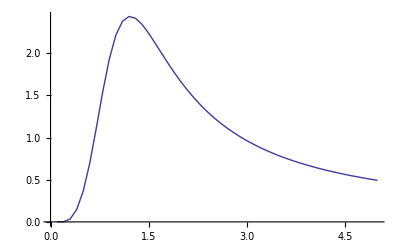

```mathematica
P1=ListPlot[Table[{t/10,10sh[t/10,3]/t},{t,1,50}],Joined->True]
```

```mathematica
shE[k_]:=Block[{c},
Clear[η,μ];
c=Factor[(dμdβ^2*D[Log[Z[k]],{μ,2}]+d2μdβ2*D[Log[Z[k]],{μ,1}])/.η->1];
Return[c/2^k];
]
```

```mathematica
shE[3]
```

(8 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/((1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)

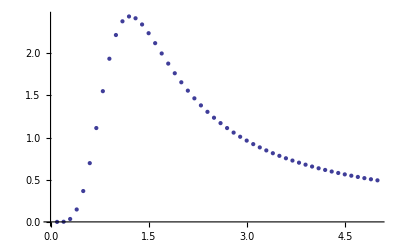

```mathematica
P2=ListPlot[Table[{t/10,10(%/.μ->Exp[-20/t])/t},{t,1,50}]]
```

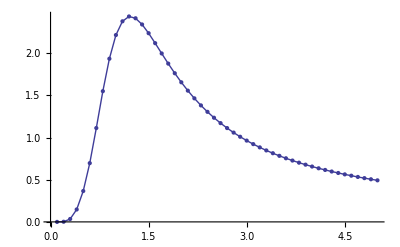

```mathematica
Show[P1,P2]
```

```mathematica
Chi[T_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},
Clear[μ,η];
InitRGΩ;
μ=N[Exp[-4/T],400];
η=1;
For[k=1,k<kmax,k++,RGΩ];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Return[(term0+term1+term2+term3)/2^kmax];
]
```

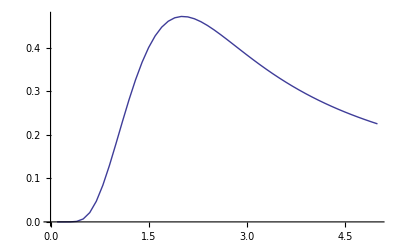

```mathematica
PX1=ListPlot[Table[{t/10,10/t*Exp[-40/t]Chi[t/10,3]},{t,1,50}],Joined->True]
```

```mathematica
ChiE[k_]:=Block[{c},
Clear[η,μ];
c=Factor[(dηdH^2*D[Log[Z[k]],{η,2}]+d2ηdH2*D[Log[Z[k]],{η,1}])/.η->1];
Return[c/2^k];
]
```

```mathematica
ChiE[3]
```

(81+196 μ+534 μ^2+668 μ^3+673 μ^4+152 μ^5)/(8 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5))

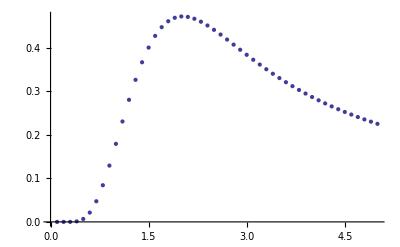

```mathematica
PX2=ListPlot[Table[{t/10,(10/t(μ*%)/.μ->Exp[-40/t])},{t,1,50}]]
```

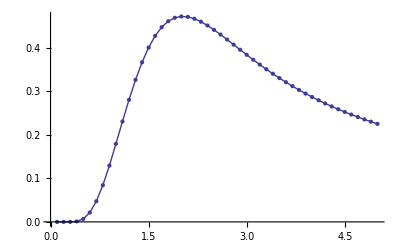

```mathematica
Show[PX1,PX2]
```

```mathematica
HierChi[T_,level_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},
Clear[μ,η];
InitRGΩ;
μ=N[Exp[-4/T],400];
η=1;
For[k=1,k<kmax,k++,If[k>level,RGΩ,RG]];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Return[(term0+term1+term2+term3)/2^(kmax-level)];
]
```

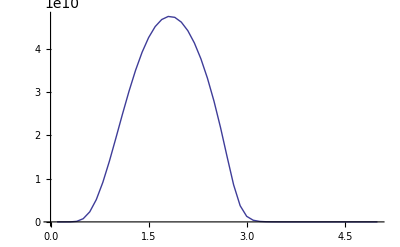

```mathematica
PX20=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,0,40]},{t,1,50}],Joined->True]
```

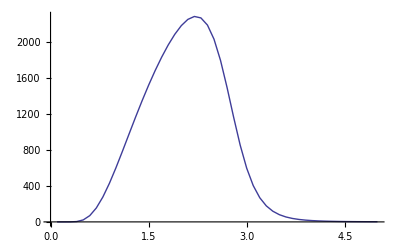

```mathematica
PX10=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,5,20]},{t,1,50}],Joined->True]
```

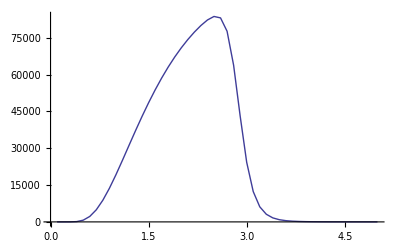

```mathematica
PX10=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,20,40]},{t,1,50}],Joined->True]
```

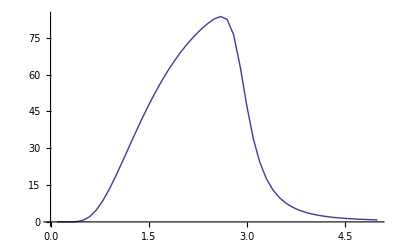

```mathematica
PX10=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,30,40]},{t,1,50}],Joined->True]
```

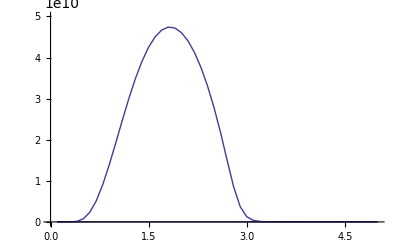

```mathematica
Show[PX10,PX20,PlotRange->{{0,5},{0,5*10^10}}]
```